```mathematica
pairswlen[list_,len_]:=Table[{list[[i]],list[[i+1]]},{i,1,len-1}]
pairs[list_]:=pairswlen[list,Length[list]]
allpairs[m_]:=Flatten[Table[{i,j},{i,1,m-1},{j,i+1,m}],1]
allpairs[3]
```

{{1,2},{1,3},{2,3}}

```mathematica
pairnum[pairlist_,{x_,y_}]:=If[x≠y,If[x<y,Position[pairlist,{x,y}],-Position[pairlist,{y,x}]],0][[1]][[1]]
pairnum[allpairs[3],{1,3}]
pairnum[allpairs[3],{3,2}]
```

2

-3

```mathematica
"remember that all in orig. cycle are given."
```

```mathematica
tovars[x_]:=Map[If[#<0,Subscript[b, -#](1-Subscript[a, -#]),Subscript[b, #](Subscript[a, #])]&,x]
tovar[x_]:=If[#<0,Subscript[b, -#](1-Subscript[a, -#]),Subscript[b, #](Subscript[a, #])]&[x]
tolist[x_]:=Table[x[[i]],{i,1,Length[x]}]
total2[x_]:=Piecewise[{{Total[x], ListQ[x]}, {x, True}}]
splitform[x_]:=Block[{list=tolist[x]},{Total[Map[If[NumberQ[#],#,If[NumberQ[First[#]],If[First[#]>0,#,0],#]]&,list]],-Total[Map[If[NumberQ[#],0,If[NumberQ[First[#]],If[First[#]>0,0,#],0]]&,list]]}]
```

```mathematica
OldAdamsForms[n_]:=
Block[{g=CompleteGraph[n]},
Block[{edges=EdgeList[g],
cy=Table[{Mod[i-1,n]+1,Mod[i,n]+1},{i,1,n}]},
Block[{pairlist=Complement[allpairs[n],cy],
fepaths=Table[FindVertexIndependentPaths[g,Mod[i-1,n]+1,Mod[i,n]+1,∞],{i,1,n}],
bepaths=Table[FindVertexIndependentPaths[g,Mod[i,n]+1,Mod[i-1,n]+1,∞],{i,1,n}]},
Block[{fppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,fepaths,{2}]],
bppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,bepaths,{2}]]},
Block[{ffpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,fppaths,{2}],{2}]]],
bfpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,bppaths,{2}],{2}]]]},
Block[{difs=Table[ffpaths[[i]]-bfpaths[[i]],{i,1,n}]},
Map[splitform,difs]]]]]]]
(*This one fails because the outer cycle alone is not enough to iff a counterexample*)
```

```mathematica
cy[d*+e]==ps[+e]
cy[d*-e]==ps[-e]

cy[d*+e]>cy[d*-e]

cy[d*+e]-cy[d*-e]==ps[+e]-ps[-e]>0
ps[+e]==ps[v'->v]
ps[-e]==ps[v->v']
```

```mathematica
AdamsForms[n_]:=
Block[{g=CompleteGraph[n]},
Block[{edges=EdgeList[g],
cy=Table[{Mod[i-1,n]+1,Mod[i,n]+1},{i,1,n}]},
Block[{pairlist=Complement[allpairs[n],cy],
fepaths=Flatten[Table[FindVertexIndependentPaths[g,i,j,∞],{i,1,n-1},{j,i+1,n}],1],
bepaths=Flatten[Table[FindVertexIndependentPaths[g,j,i,∞],{i,1,n-1},{j,i+1,n}],1]},
Block[{fppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,fepaths,{2}]],
bppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,bepaths,{2}]]},
Block[{ffpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,fppaths,{2}],{2}]]],
bfpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,bppaths,{2}],{2}]]]},
Block[{difs=Table[ffpaths[[i]]-bfpaths[[i]],{i,1,Length[ffpaths]}]},
Map[splitform,difs]]]]]]]
(*Each output pair {f,b} -> f-b must be greater than zero for the assignments to give a counterexample*)
```

```mathematica
f<b
f-b<0
p-n<0
p<n
```

```mathematica
enum[x_]:=If[Length[x]<1,x,Table[Join[{i},x[[i]]],{i,1,Length[x]}]]
```

```mathematica
pairenum[x_]:=If[Length[x]<1,x,
Block[{n=Ceiling[1/2 (+1+√(1+8 Length[x]))]},Block[{pairlist=tuples[n]},Table[Flatten[Join[{pairlist[[i]]},x[[i]]]],{i,1,Length[x]}]]]]
```

```mathematica
pairenum[{1,2,3,4,5,6,7,8,9,10,11}]
```

{{{1,2},1},{{1,3},2},{{1,4},3},{{1,5},4},{{1,6},5},{{2,3},6},{{2,4},7},{{2,5},8},{{2,6},9},{{3,4},10},{{3,5},11}}

```mathematica
tuples[n_]:=Flatten[Table[{i,j},{i,1,n-1},{j,i+1,n}],1]
tuples[3]
Table[Length[tuples[n]],{n,2,10}]
FullSimplify[InterpolatingPolynomial[%,n]]
```

{{1,2},{1,3},{2,3}}

{1,3,6,10,15,21,28,36,45}

1/2 n (1+n)

```mathematica
FullSimplify[-1/2+1/2 √(1+8 m)]
```

1/2 (-1+√(1+8 m))

```mathematica
Reduce[{1/2 n (1+n)==m,m≥2,n≥1},n]
```

m≥2&&n==-1/2+1/2 √(1+8 m)

```mathematica
pairenum[AdamsForms[3]]//TableForm
```

1 | 2 | 1+2 a_1 b_1 | b_1
1 | 3 | 1+2 a_1 b_1 | b_1
2 | 3 | 1+2 a_1 b_1 | b_1

```mathematica
enum[AdamsForms[3]]
```

{{1,1+2 a_1 b_1,b_1},{2,1+2 a_1 b_1,b_1},{3,1+2 a_1 b_1,b_1}}

```mathematica
pairenum[AdamsForms[3]]//TableForm
```

1 | 2 | 1+2 a_1 b_1 | b_1
1 | 3 | 1+2 a_1 b_1 | b_1
2 | 3 | 1+2 a_1 b_1 | b_1

```mathematica
pairenum[AdamsForms[4]]//TableForm
```

1 | 2 | 1+2 a_1 b_1+a_2 b_2 b_3 | b_1+a_3 b_2 b_3
1 | 3 | 1+2 a_1 b_1+2 a_2 b_2 | b_1+b_2
1 | 4 | 2 a_1 b_1+2 a_2 b_2+2 a_3 b_3 | b_1+b_2+b_3
2 | 3 | 1+2 a_1 b_1+2 a_3 b_3 | b_1+b_3
2 | 4 | 1+2 a_2 b_2+2 a_3 b_3 | b_2+b_3
3 | 4 | 1+a_2 b_1 b_2+2 a_3 b_3 | a_1 b_1 b_2+b_3

```mathematica
pairenum[AdamsForms[5]]//TableForm
```

1 | 2 | 1+2 a_1 b_1+a_2 b_2 b_4+a_3 b_3 b_5 | b_1+a_4 b_2 b_4+a_5 b_3 b_5
1 | 3 | 1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_6 | b_1+b_2+a_6 b_3 b_6
1 | 4 | 2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4 | b_1+b_2+b_3+b_4
1 | 5 | 2 a_2 b_2+2 a_3 b_3+2 a_5 b_5+a_1 b_1 b_6+a_6 b_1 b_6 | b_2+b_3+b_5+b_1 b_6
2 | 3 | 1+2 a_1 b_1+2 a_4 b_4+a_5 b_5 b_6 | b_1+b_4+a_6 b_5 b_6
2 | 4 | 1+2 a_2 b_2+2 a_4 b_4+2 a_5 b_5 | b_2+b_4+b_5
2 | 5 | 2 a_3 b_3+2 a_4 b_4+2 a_5 b_5+2 a_6 b_6 | b_3+b_4+b_5+b_6
3 | 4 | 1+a_2 b_1 b_2+2 a_4 b_4+2 a_6 b_6 | a_1 b_1 b_2+b_4+b_6
3 | 5 | 1+a_3 b_1 b_3+2 a_5 b_5+2 a_6 b_6 | a_1 b_1 b_3+b_5+b_6
4 | 5 | 1+a_3 b_2 b_3+a_5 b_4 b_5+2 a_6 b_6 | a_2 b_2 b_3+a_4 b_4 b_5+b_6

```mathematica
BooleanMinimize[((b2&&b3)||(b4&&b5)||b6)&&((b1&&b3)||b5||b6)&&((b1&&b2)||b4||b6)&&(b3||b4||b5||b6)&&(b2||b4||b5)&&(b1||b4||(b5&&b6))&&(b2||b3||b5||(b1&&b6))&&(b1||b2||b3||b4)&&(b1||b2||(b3&&b6))&&(b1||(b2&&b4)||(b3&&b5))]
```

(b1&&b2&&b3)||(b1&&b2&&b6)||(b1&&b4&&b5)||(b1&&b4&&b6)||(b1&&b5&&b6)||(b2&&b4&&b5)||(b2&&b4&&b6)||(b3&&b5&&b6)

```mathematica
pairenum[AdamsForms[6]]//TableForm
```

1 | 2 | 1+2 a_1 b_1+a_2 b_2 b_5+a_3 b_3 b_6+a_4 b_4 b_7 | b_1+a_5 b_2 b_5+a_6 b_3 b_6+a_7 b_4 b_7
1 | 3 | 1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_8+a_4 b_4 b_9 | b_1+b_2+a_8 b_3 b_8+a_9 b_4 b_9
1 | 4 | 2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_5 b_5+a_4 b_4 b_10 | b_1+b_2+b_3+b_5+a_10 b_4 b_10
1 | 5 | 2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_6 b_6+a_1 b_1 b_8+a_8 b_1 b_8 | b_2+b_3+b_4+b_6+b_1 b_8
1 | 6 | 2 a_3 b_3+2 a_4 b_4+2 a_7 b_7+a_1 b_1 b_9+a_9 b_1 b_9+a_2 b_2 b_10+a_10 b_2 b_10 | b_3+b_4+b_7+b_1 b_9+b_2 b_10
2 | 3 | 1+2 a_1 b_1+2 a_5 b_5+a_6 b_6 b_8+a_7 b_7 b_9 | b_1+b_5+a_8 b_6 b_8+a_9 b_7 b_9
2 | 4 | 1+2 a_2 b_2+2 a_5 b_5+2 a_6 b_6+a_7 b_7 b_10 | b_2+b_5+b_6+a_10 b_7 b_10
2 | 5 | 2 a_3 b_3+2 a_5 b_5+2 a_6 b_6+2 a_7 b_7+2 a_8 b_8 | b_3+b_5+b_6+b_7+b_8
2 | 6 | 2 a_4 b_4+2 a_6 b_6+2 a_7 b_7+2 a_9 b_9+a_5 b_5 b_10+a_10 b_5 b_10 | b_4+b_6+b_7+b_9+b_5 b_10
3 | 4 | 1+a_2 b_1 b_2+2 a_5 b_5+2 a_8 b_8+a_9 b_9 b_10 | a_1 b_1 b_2+b_5+b_8+a_10 b_9 b_10
3 | 5 | 1+a_3 b_1 b_3+2 a_6 b_6+2 a_8 b_8+2 a_9 b_9 | a_1 b_1 b_3+b_6+b_8+b_9
3 | 6 | a_4 b_1 b_4+2 a_7 b_7+2 a_8 b_8+2 a_9 b_9+2 a_10 b_10 | a_1 b_1 b_4+b_7+b_8+b_9+b_10
4 | 5 | 1+a_3 b_2 b_3+a_6 b_5 b_6+2 a_8 b_8+2 a_10 b_10 | a_2 b_2 b_3+a_5 b_5 b_6+b_8+b_10
4 | 6 | 1+a_4 b_2 b_4+a_7 b_5 b_7+2 a_9 b_9+2 a_10 b_10 | a_2 b_2 b_4+a_5 b_5 b_7+b_9+b_10
5 | 6 | 1+a_4 b_3 b_4+a_7 b_6 b_7+a_9 b_8 b_9+2 a_10 b_10 | a_3 b_3 b_4+a_6 b_6 b_7+a_8 b_8 b_9+b_10

```mathematica
pairenum[AdamsForms[7]]//TableForm
```

1 | 2 | 1+2 a_1 b_1+a_2 b_2 b_6+a_3 b_3 b_7+a_4 b_4 b_8+a_5 b_5 b_9 | b_1+a_6 b_2 b_6+a_7 b_3 b_7+a_8 b_4 b_8+a_9 b_5 b_9
1 | 3 | 1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_10+a_4 b_4 b_11+a_5 b_5 b_12 | b_1+b_2+a_10 b_3 b_10+a_11 b_4 b_11+a_12 b_5 b_12
1 | 4 | 2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_6 b_6+a_4 b_4 b_13+a_5 b_5 b_14 | b_1+b_2+b_3+b_6+a_13 b_4 b_13+a_14 b_5 b_14
1 | 5 | 2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_7 b_7+a_1 b_1 b_10+a_10 b_1 b_10+a_5 b_5 b_15 | b_2+b_3+b_4+b_7+b_1 b_10+a_15 b_5 b_15
1 | 6 | 2 a_3 b_3+2 a_4 b_4+2 a_5 b_5+2 a_8 b_8+a_1 b_1 b_11+a_11 b_1 b_11+a_2 b_2 b_13+a_13 b_2 b_13 | b_3+b_4+b_5+b_8+b_1 b_11+b_2 b_13
1 | 7 | 2 a_4 b_4+2 a_5 b_5+2 a_9 b_9+a_1 b_1 b_12+a_12 b_1 b_12+a_2 b_2 b_14+a_14 b_2 b_14+a_3 b_3 b_15+a_15 b_3 b_15 | b_4+b_5+b_9+b_1 b_12+b_2 b_14+b_3 b_15
2 | 3 | 1+2 a_1 b_1+2 a_6 b_6+a_7 b_7 b_10+a_8 b_8 b_11+a_9 b_9 b_12 | b_1+b_6+a_10 b_7 b_10+a_11 b_8 b_11+a_12 b_9 b_12
2 | 4 | 1+2 a_2 b_2+2 a_6 b_6+2 a_7 b_7+a_8 b_8 b_13+a_9 b_9 b_14 | b_2+b_6+b_7+a_13 b_8 b_13+a_14 b_9 b_14
2 | 5 | 2 a_3 b_3+2 a_6 b_6+2 a_7 b_7+2 a_8 b_8+2 a_10 b_10+a_9 b_9 b_15 | b_3+b_6+b_7+b_8+b_10+a_15 b_9 b_15
2 | 6 | 2 a_4 b_4+2 a_7 b_7+2 a_8 b_8+2 a_9 b_9+2 a_11 b_11+a_6 b_6 b_13+a_13 b_6 b_13 | b_4+b_7+b_8+b_9+b_11+b_6 b_13
2 | 7 | 2 a_5 b_5+2 a_8 b_8+2 a_9 b_9+2 a_12 b_12+a_6 b_6 b_14+a_14 b_6 b_14+a_7 b_7 b_15+a_15 b_7 b_15 | b_5+b_8+b_9+b_12+b_6 b_14+b_7 b_15
3 | 4 | 1+a_2 b_1 b_2+2 a_6 b_6+2 a_10 b_10+a_11 b_11 b_13+a_12 b_12 b_14 | a_1 b_1 b_2+b_6+b_10+a_13 b_11 b_13+a_14 b_12 b_14
3 | 5 | 1+a_3 b_1 b_3+2 a_7 b_7+2 a_10 b_10+2 a_11 b_11+a_12 b_12 b_15 | a_1 b_1 b_3+b_7+b_10+b_11+a_15 b_12 b_15
3 | 6 | a_4 b_1 b_4+2 a_8 b_8+2 a_10 b_10+2 a_11 b_11+2 a_12 b_12+2 a_13 b_13 | a_1 b_1 b_4+b_8+b_10+b_11+b_12+b_13
3 | 7 | a_5 b_1 b_5+2 a_9 b_9+2 a_11 b_11+2 a_12 b_12+2 a_14 b_14+a_10 b_10 b_15+a_15 b_10 b_15 | a_1 b_1 b_5+b_9+b_11+b_12+b_14+b_10 b_15
4 | 5 | 1+a_3 b_2 b_3+a_7 b_6 b_7+2 a_10 b_10+2 a_13 b_13+a_14 b_14 b_15 | a_2 b_2 b_3+a_6 b_6 b_7+b_10+b_13+a_15 b_14 b_15
4 | 6 | 1+a_4 b_2 b_4+a_8 b_6 b_8+2 a_11 b_11+2 a_13 b_13+2 a_14 b_14 | a_2 b_2 b_4+a_6 b_6 b_8+b_11+b_13+b_14
4 | 7 | a_5 b_2 b_5+a_9 b_6 b_9+2 a_12 b_12+2 a_13 b_13+2 a_14 b_14+2 a_15 b_15 | a_2 b_2 b_5+a_6 b_6 b_9+b_12+b_13+b_14+b_15
5 | 6 | 1+a_4 b_3 b_4+a_8 b_7 b_8+a_11 b_10 b_11+2 a_13 b_13+2 a_15 b_15 | a_3 b_3 b_4+a_7 b_7 b_8+a_10 b_10 b_11+b_13+b_15
5 | 7 | 1+a_5 b_3 b_5+a_9 b_7 b_9+a_12 b_10 b_12+2 a_14 b_14+2 a_15 b_15 | a_3 b_3 b_5+a_7 b_7 b_9+a_10 b_10 b_12+b_14+b_15
6 | 7 | 1+a_5 b_4 b_5+a_9 b_8 b_9+a_12 b_11 b_12+a_14 b_13 b_14+2 a_15 b_15 | a_4 b_4 b_5+a_8 b_8 b_9+a_11 b_11 b_12+a_13 b_13 b_14+b_15

```mathematica
pairenum[AdamsForms[8]]//TableForm
```

1 | 2 | 1+2 a_1 b_1+a_2 b_2 b_7+a_3 b_3 b_8+a_4 b_4 b_9+a_5 b_5 b_10+a_6 b_6 b_11 | b_1+a_7 b_2 b_7+a_8 b_3 b_8+a_9 b_4 b_9+a_10 b_5 b_10+a_11 b_6 b_11
1 | 3 | 1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_12+a_4 b_4 b_13+a_5 b_5 b_14+a_6 b_6 b_15 | b_1+b_2+a_12 b_3 b_12+a_13 b_4 b_13+a_14 b_5 b_14+a_15 b_6 b_15
1 | 4 | 2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_7 b_7+a_4 b_4 b_16+a_5 b_5 b_17+a_6 b_6 b_18 | b_1+b_2+b_3+b_7+a_16 b_4 b_16+a_17 b_5 b_17+a_18 b_6 b_18
1 | 5 | 2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_8 b_8+a_1 b_1 b_12+a_12 b_1 b_12+a_5 b_5 b_19+a_6 b_6 b_20 | b_2+b_3+b_4+b_8+b_1 b_12+a_19 b_5 b_19+a_20 b_6 b_20
1 | 6 | 2 a_3 b_3+2 a_4 b_4+2 a_5 b_5+2 a_9 b_9+a_1 b_1 b_13+a_13 b_1 b_13+a_2 b_2 b_16+a_16 b_2 b_16+a_6 b_6 b_21 | b_3+b_4+b_5+b_9+b_1 b_13+b_2 b_16+a_21 b_6 b_21
1 | 7 | 2 a_4 b_4+2 a_5 b_5+2 a_6 b_6+2 a_10 b_10+a_1 b_1 b_14+a_14 b_1 b_14+a_2 b_2 b_17+a_17 b_2 b_17+a_3 b_3 b_19+a_19 b_3 b_19 | b_4+b_5+b_6+b_10+b_1 b_14+b_2 b_17+b_3 b_19
1 | 8 | 2 a_5 b_5+2 a_6 b_6+2 a_11 b_11+a_1 b_1 b_15+a_15 b_1 b_15+a_2 b_2 b_18+a_18 b_2 b_18+a_3 b_3 b_20+a_20 b_3 b_20+a_4 b_4 b_21+a_21 b_4 b_21 | b_5+b_6+b_11+b_1 b_15+b_2 b_18+b_3 b_20+b_4 b_21
2 | 3 | 1+2 a_1 b_1+2 a_7 b_7+a_8 b_8 b_12+a_9 b_9 b_13+a_10 b_10 b_14+a_11 b_11 b_15 | b_1+b_7+a_12 b_8 b_12+a_13 b_9 b_13+a_14 b_10 b_14+a_15 b_11 b_15
2 | 4 | 1+2 a_2 b_2+2 a_7 b_7+2 a_8 b_8+a_9 b_9 b_16+a_10 b_10 b_17+a_11 b_11 b_18 | b_2+b_7+b_8+a_16 b_9 b_16+a_17 b_10 b_17+a_18 b_11 b_18
2 | 5 | 2 a_3 b_3+2 a_7 b_7+2 a_8 b_8+2 a_9 b_9+2 a_12 b_12+a_10 b_10 b_19+a_11 b_11 b_20 | b_3+b_7+b_8+b_9+b_12+a_19 b_10 b_19+a_20 b_11 b_20
2 | 6 | 2 a_4 b_4+2 a_8 b_8+2 a_9 b_9+2 a_10 b_10+2 a_13 b_13+a_7 b_7 b_16+a_16 b_7 b_16+a_11 b_11 b_21 | b_4+b_8+b_9+b_10+b_13+b_7 b_16+a_21 b_11 b_21
2 | 7 | 2 a_5 b_5+2 a_9 b_9+2 a_10 b_10+2 a_11 b_11+2 a_14 b_14+a_7 b_7 b_17+a_17 b_7 b_17+a_8 b_8 b_19+a_19 b_8 b_19 | b_5+b_9+b_10+b_11+b_14+b_7 b_17+b_8 b_19
2 | 8 | 2 a_6 b_6+2 a_10 b_10+2 a_11 b_11+2 a_15 b_15+a_7 b_7 b_18+a_18 b_7 b_18+a_8 b_8 b_20+a_20 b_8 b_20+a_9 b_9 b_21+a_21 b_9 b_21 | b_6+b_10+b_11+b_15+b_7 b_18+b_8 b_20+b_9 b_21
3 | 4 | 1+a_2 b_1 b_2+2 a_7 b_7+2 a_12 b_12+a_13 b_13 b_16+a_14 b_14 b_17+a_15 b_15 b_18 | a_1 b_1 b_2+b_7+b_12+a_16 b_13 b_16+a_17 b_14 b_17+a_18 b_15 b_18
3 | 5 | 1+a_3 b_1 b_3+2 a_8 b_8+2 a_12 b_12+2 a_13 b_13+a_14 b_14 b_19+a_15 b_15 b_20 | a_1 b_1 b_3+b_8+b_12+b_13+a_19 b_14 b_19+a_20 b_15 b_20
3 | 6 | a_4 b_1 b_4+2 a_9 b_9+2 a_12 b_12+2 a_13 b_13+2 a_14 b_14+2 a_16 b_16+a_15 b_15 b_21 | a_1 b_1 b_4+b_9+b_12+b_13+b_14+b_16+a_21 b_15 b_21
3 | 7 | a_5 b_1 b_5+2 a_10 b_10+2 a_13 b_13+2 a_14 b_14+2 a_15 b_15+2 a_17 b_17+a_12 b_12 b_19+a_19 b_12 b_19 | a_1 b_1 b_5+b_10+b_13+b_14+b_15+b_17+b_12 b_19
3 | 8 | a_6 b_1 b_6+2 a_11 b_11+2 a_14 b_14+2 a_15 b_15+2 a_18 b_18+a_12 b_12 b_20+a_20 b_12 b_20+a_13 b_13 b_21+a_21 b_13 b_21 | a_1 b_1 b_6+b_11+b_14+b_15+b_18+b_12 b_20+b_13 b_21
4 | 5 | 1+a_3 b_2 b_3+a_8 b_7 b_8+2 a_12 b_12+2 a_16 b_16+a_17 b_17 b_19+a_18 b_18 b_20 | a_2 b_2 b_3+a_7 b_7 b_8+b_12+b_16+a_19 b_17 b_19+a_20 b_18 b_20
4 | 6 | 1+a_4 b_2 b_4+a_9 b_7 b_9+2 a_13 b_13+2 a_16 b_16+2 a_17 b_17+a_18 b_18 b_21 | a_2 b_2 b_4+a_7 b_7 b_9+b_13+b_16+b_17+a_21 b_18 b_21
4 | 7 | a_5 b_2 b_5+a_10 b_7 b_10+2 a_14 b_14+2 a_16 b_16+2 a_17 b_17+2 a_18 b_18+2 a_19 b_19 | a_2 b_2 b_5+a_7 b_7 b_10+b_14+b_16+b_17+b_18+b_19
4 | 8 | a_6 b_2 b_6+a_11 b_7 b_11+2 a_15 b_15+2 a_17 b_17+2 a_18 b_18+2 a_20 b_20+a_16 b_16 b_21+a_21 b_16 b_21 | a_2 b_2 b_6+a_7 b_7 b_11+b_15+b_17+b_18+b_20+b_16 b_21
5 | 6 | 1+a_4 b_3 b_4+a_9 b_8 b_9+a_13 b_12 b_13+2 a_16 b_16+2 a_19 b_19+a_20 b_20 b_21 | a_3 b_3 b_4+a_8 b_8 b_9+a_12 b_12 b_13+b_16+b_19+a_21 b_20 b_21
5 | 7 | 1+a_5 b_3 b_5+a_10 b_8 b_10+a_14 b_12 b_14+2 a_17 b_17+2 a_19 b_19+2 a_20 b_20 | a_3 b_3 b_5+a_8 b_8 b_10+a_12 b_12 b_14+b_17+b_19+b_20
5 | 8 | a_6 b_3 b_6+a_11 b_8 b_11+a_15 b_12 b_15+2 a_18 b_18+2 a_19 b_19+2 a_20 b_20+2 a_21 b_21 | a_3 b_3 b_6+a_8 b_8 b_11+a_12 b_12 b_15+b_18+b_19+b_20+b_21
6 | 7 | 1+a_5 b_4 b_5+a_10 b_9 b_10+a_14 b_13 b_14+a_17 b_16 b_17+2 a_19 b_19+2 a_21 b_21 | a_4 b_4 b_5+a_9 b_9 b_10+a_13 b_13 b_14+a_16 b_16 b_17+b_19+b_21
6 | 8 | 1+a_6 b_4 b_6+a_11 b_9 b_11+a_15 b_13 b_15+a_18 b_16 b_18+2 a_20 b_20+2 a_21 b_21 | a_4 b_4 b_6+a_9 b_9 b_11+a_13 b_13 b_15+a_16 b_16 b_18+b_20+b_21
7 | 8 | 1+a_6 b_5 b_6+a_11 b_10 b_11+a_15 b_14 b_15+a_18 b_17 b_18+a_20 b_19 b_20+2 a_21 b_21 | a_5 b_5 b_6+a_10 b_10 b_11+a_14 b_14 b_15+a_17 b_17 b_18+a_19 b_19 b_20+b_21

```mathematica
pairenum[AdamsForms[9]]//TableForm
```

```mathematica
afs=Table[AdamsForms[i],{i,3,15}];
```

```mathematica
tolistif[list_]:=Piecewise[{{tolist[list], Length[list]>0}, {list, True}}]
```

```mathematica
form2trips[form_]:=Map[{#[[1]],#[[2]][[2]],#[[3]][[2]],#[[4]][[2]]}&,Map[Piecewise[{{Join[{1,{a,0}},#], Length[#]==2}, {Join[{1},#], Length[#]==3}, {#, True}}]&,Map[If[ToString[First[#]]=="b",{1,{a,0},#,{b,0}},#]&,Map[If[NumberQ[First[#]]&&Length[#]==3,Join[#,{{b,0}}],#]&,Map[If[Length[#]==0,{#,{a,0},{b,0},{b,0}},#]&,Map[tolistif,Map[tolistif,tolist[form]],{2}]]]]]]
```

```mathematica
First[Flatten[afs[[3]]]]
form2trips[%]
```

1+2 a_1 b_1+a_2 b_2 b_4+a_3 b_3 b_5

{{1,0,0,0},{2,1,1,0},{1,2,2,4},{1,3,3,5}}

```mathematica
formcoefficient[x_]:=If[NumberQ[x],x,If[NumberQ[First[x]],First[x],1]]
```

```mathematica
Map[Length,afs[[3]],{2}]
{Max[Map[First,%]],Max[Map[Last,%]]}
```

{{4,3},{4,3},{4,4},{5,4},{4,3},{4,3},{4,4},{4,3},{4,3},{4,3}}

{5,4}

```mathematica
all2sPosition[forms_]:=Flatten[Position[Map[DeleteDuplicates,Map[First,Map[Map[formcoefficient,Map[tolist,#,{1}],{2}]&,forms]]],{2}]]
```

```mathematica
Table[{i,all2sPosition[AdamsForms[i]]},{i,4,15}]//Column
```

{4,{3}}
{5,{3,7}}
{6,{8}}
{7,{}}
{8,{}}
{9,{}}
{10,{}}
{11,{}}
{12,{}}
{13,{}}
{14,{}}
{15,{}}

```mathematica
Map[formcoefficient,tolist[afs[[3]][[1]][[1]]]]
```

{1,2,1,1}

```mathematica
formscoefficientarray[forms_]:=Block[{lengths=Map[Length,forms,{2}]},
Block[{maxlengths={Max[Map[First,lengths]],Max[Map[Last,lengths]]}},
Block[{bools=Map[boolecoefficient,Map[tolist,forms,{2}],{3}]},
Map[Flatten,Map[{PadLeft[#[[1]],maxlengths[[1]]],PadLeft[#[[2]],maxlengths[[2]]]}&,bools]]]]]
```

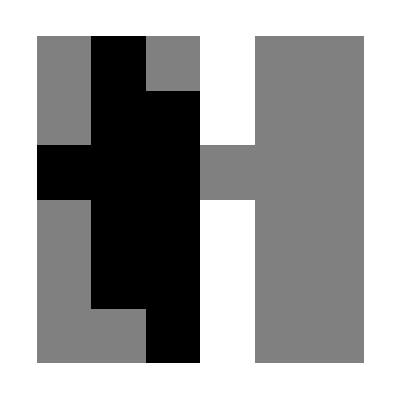
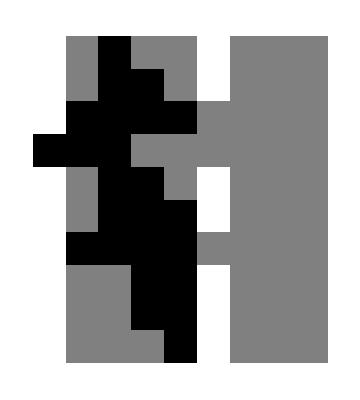
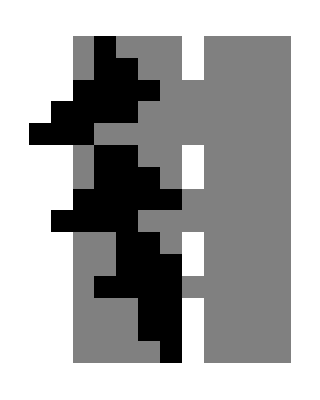
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[formscoefficientarray[AdamsForms[i]]],{i,4,15}]
```

```mathematica
ListPlot[Flatten[Map[form2trips[#]&,Flatten[afs[[8]]]],1],Joined->True]
```

```mathematica
triptable[n_]:={Table[{i,Sort[form2trips[AdamsForms[n][[i]][[1]]]]},{i,1,(n-1)(n-2)/2}],Table[{i,form2trips[AdamsForms[n][[i]][[2]]]},{i,1,(n-1)(n-2)/2}]}//TableForm
```

```mathematica
triptable[4]
```

1 |  | 
1
0
0
0 | 1
2
2
3 | 2
1
1
0 | 2 |  | 
1
0
0
0 | 2
1
1
0 | 2
2
2
0 | 3 |  | 
2
1
1
0 | 2
2
2
0 | 2
3
3
0
1 | 
1
0
1
0 | 1
3
2
3 | 2 | 
1
0
1
0 | 1
0
2
0 | 3 |  | 
1
0
1
0 | 1
0
2
0 | 1
0
3
0

```mathematica
triptable[5]
```

1 |  |  | 
1
0
0
0 | 1
2
2
4 | 1
3
3
5 | 2
1
1
0 | 2 |  |  | 
1
0
0
0 | 1
3
3
6 | 2
1
1
0 | 2
2
2
0 | 3 |  |  | 
2
1
1
0 | 2
2
2
0 | 2
3
3
0 | 2
4
4
0 | 4 |  |  |  | 
1
1
1
6 | 1
6
1
6 | 2
2
2
0 | 2
3
3
0 | 2
5
5
0 | 5 |  |  | 
1
0
0
0 | 1
5
5
6 | 2
1
1
0 | 2
4
4
0 | 6 |  |  | 
1
0
0
0 | 2
2
2
0 | 2
4
4
0 | 2
5
5
0
1 |  | 
1
0
1
0 | 1
4
2
4 | 1
5
3
5 | 2 |  | 
1
0
1
0 | 1
0
2
0 | 1
6
3
6 | 3 |  |  | 
1
0
1
0 | 1
0
2
0 | 1
0
3
0 | 1
0
4
0 | 4 |  |  | 
1
0
2
0 | 1
0
3
0 | 1
0
5
0 | 1
0
1
6 | 5 |  | 
1
0
1
0 | 1
0
4
0 | 1
6
5
6 | 6 |  | 
1
0
2
0 | 1
0
4
0 | 1
0
5
0

```mathematica
triptable[6]
```

1 |  |  |  | 
1
0
0
0 | 1
2
2
5 | 1
3
3
6 | 1
4
4
7 | 2
1
1
0 | 2 |  |  |  | 
1
0
0
0 | 1
3
3
8 | 1
4
4
9 | 2
1
1
0 | 2
2
2
0 | 3 |  |  |  | 
1
4
4
10 | 2
1
1
0 | 2
2
2
0 | 2
3
3
0 | 2
5
5
0 | 4 |  |  |  |  | 
1
1
1
8 | 1
8
1
8 | 2
2
2
0 | 2
3
3
0 | 2
4
4
0 | 2
6
6
0 | 5 |  |  |  |  |  | 
1
1
1
9 | 1
2
2
10 | 1
9
1
9 | 1
10
2
10 | 2
3
3
0 | 2
4
4
0 | 2
7
7
0 | 6 |  |  |  | 
1
0
0
0 | 1
6
6
8 | 1
7
7
9 | 2
1
1
0 | 2
5
5
0 | 7 |  |  |  | 
1
0
0
0 | 1
7
7
10 | 2
2
2
0 | 2
5
5
0 | 2
6
6
0 | 8 |  |  |  | 
2
3
3
0 | 2
5
5
0 | 2
6
6
0 | 2
7
7
0 | 2
8
8
0 | 9 |  |  |  |  | 
1
5
5
10 | 1
10
5
10 | 2
4
4
0 | 2
6
6
0 | 2
7
7
0 | 2
9
9
0 | 10 |  |  |  | 
1
0
0
0 | 1
2
1
2 | 1
9
9
10 | 2
5
5
0 | 2
8
8
0
1 |  |  | 
1
0
1
0 | 1
5
2
5 | 1
6
3
6 | 1
7
4
7 | 2 |  |  | 
1
0
1
0 | 1
0
2
0 | 1
8
3
8 | 1
9
4
9 | 3 |  |  |  | 
1
0
1
0 | 1
0
2
0 | 1
0
3
0 | 1
0
5
0 | 1
10
4
10 | 4 |  |  |  | 
1
0
2
0 | 1
0
3
0 | 1
0
4
0 | 1
0
6
0 | 1
0
1
8 | 5 |  |  |  | 
1
0
3
0 | 1
0
4
0 | 1
0
7
0 | 1
0
1
9 | 1
0
2
10 | 6 |  |  | 
1
0
1
0 | 1
0
5
0 | 1
8
6
8 | 1
9
7
9 | 7 |  |  | 
1
0
2
0 | 1
0
5
0 | 1
0
6
0 | 1
10
7
10 | 8 |  |  |  | 
1
0
3
0 | 1
0
5
0 | 1
0
6
0 | 1
0
7
0 | 1
0
8
0 | 9 |  |  |  | 
1
0
4
0 | 1
0
6
0 | 1
0
7
0 | 1
0
9
0 | 1
0
5
10 | 10 |  |  | 
1
1
1
2 | 1
0
5
0 | 1
0
8
0 | 1
10
9
10

```mathematica
Length[AdamsForms[4]]
```

6

```mathematica
Map[form2trips,AdamsForms[4],{2}]//Column
```

{{{1,0,0,0},{2,1,1,0},{1,2,2,3}},{{1,0,1,0},{1,3,2,3}}}
{{{1,0,0,0},{2,1,1,0},{2,2,2,0}},{{1,0,1,0},{1,0,2,0}}}
{{{2,1,1,0},{2,2,2,0},{2,3,3,0}},{{1,0,1,0},{1,0,2,0},{1,0,3,0}}}
{{{1,0,0,0},{2,1,1,0},{2,3,3,0}},{{1,0,1,0},{1,0,3,0}}}
{{{1,0,0,0},{2,2,2,0},{2,3,3,0}},{{1,0,2,0},{1,0,3,0}}}
{{{1,0,0,0},{1,2,1,2},{2,3,3,0}},{{1,1,1,2},{1,0,3,0}}}

```mathematica
EnumAt[list_,at_,from_]:=Table[{at,from-1+i0,list[[i0]]},{i0,1,Length[list]}]
```

```mathematica
Column[Table[{i+2,form2trips[afs[[i]][[2]][[2]]]},{i,2,8}],Alignment->","]
```

{4,{{1,0,1,0},{1,0,2,0}}}
{5,{{1,0,1,0},{1,0,2,0},{1,6,3,6}}}
{6,{{1,0,1,0},{1,0,2,0},{1,8,3,8},{1,9,4,9}}}
{7,{{1,0,1,0},{1,0,2,0},{1,10,3,10},{1,11,4,11},{1,12,5,12}}}
{8,{{1,0,1,0},{1,0,2,0},{1,12,3,12},{1,13,4,13},{1,14,5,14},{1,15,6,15}}}
{9,{{1,0,1,0},{1,0,2,0},{1,14,3,14},{1,15,4,15},{1,16,5,16},{1,17,6,17},{1,18,7,18}}}
{10,{{1,0,1,0},{1,0,2,0},{1,16,3,16},{1,17,4,17},{1,18,5,18},{1,19,6,19},{1,20,7,20},{1,21,8,21}}}

```mathematica
Column[Table[{i+2,afs[[i]][[4]][[2]]},{i,2,10}],Alignment->","]
```

{4,b_1+b_3}
{5,b_2+b_3+b_5+b_1 b_6}
{6,b_2+b_3+b_4+b_6+b_1 b_8}
{7,b_2+b_3+b_4+b_7+b_1 b_10+a_15 b_5 b_15}
{8,b_2+b_3+b_4+b_8+b_1 b_12+a_19 b_5 b_19+a_20 b_6 b_20}
{9,b_2+b_3+b_4+b_9+b_1 b_14+a_23 b_5 b_23+a_24 b_6 b_24+a_25 b_7 b_25}
{10,b_2+b_3+b_4+b_10+b_1 b_16+a_27 b_5 b_27+a_28 b_6 b_28+a_29 b_7 b_29+a_30 b_8 b_30}
{11,b_2+b_3+b_4+b_11+b_1 b_18+a_31 b_5 b_31+a_32 b_6 b_32+a_33 b_7 b_33+a_34 b_8 b_34+a_35 b_9 b_35}
{12,b_2+b_3+b_4+b_12+b_1 b_20+a_35 b_5 b_35+a_36 b_6 b_36+a_37 b_7 b_37+a_38 b_8 b_38+a_39 b_9 b_39+a_40 b_10 b_40}

```mathematica
Expand[InterpolatingPolynomial[{{6,7},{7,10}},n]]
```

-11+3 n

```mathematica
2n+2
```

```mathematica
Column[Table[{n,Subscript[b, 2]+Subscript[b, 3]+Subscript[b, 4]+Subscript[b, n]+Subscript[b, 1] Subscript[b, 2n-4]+∑_(i=5)^(n-2) Subscript[a, i+4n-18] Subscript[b, i] Subscript[b, i+4n-18]},{n,4,12}],Alignment->","]
```

{4,b_2+b_3+2 b_4+b_1 b_4}
{5,b_2+b_3+b_4+b_5+b_1 b_6}
{6,b_2+b_3+b_4+b_6+b_1 b_8}
{7,b_2+b_3+b_4+b_7+b_1 b_10+a_15 b_5 b_15}
{8,b_2+b_3+b_4+b_8+b_1 b_12+a_19 b_5 b_19+a_20 b_6 b_20}
{9,b_2+b_3+b_4+b_9+b_1 b_14+a_23 b_5 b_23+a_24 b_6 b_24+a_25 b_7 b_25}
{10,b_2+b_3+b_4+b_10+b_1 b_16+a_27 b_5 b_27+a_28 b_6 b_28+a_29 b_7 b_29+a_30 b_8 b_30}
{11,b_2+b_3+b_4+b_11+b_1 b_18+a_31 b_5 b_31+a_32 b_6 b_32+a_33 b_7 b_33+a_34 b_8 b_34+a_35 b_9 b_35}
{12,b_2+b_3+b_4+b_12+b_1 b_20+a_35 b_5 b_35+a_36 b_6 b_36+a_37 b_7 b_37+a_38 b_8 b_38+a_39 b_9 b_39+a_40 b_10 b_40}

```mathematica
Column[Table[{i+2,afs[[i]][[4]][[1]]},{i,2,10}],Alignment->","]
```

{4,1+2 a_1 b_1+2 a_3 b_3}
{5,2 a_2 b_2+2 a_3 b_3+2 a_5 b_5+a_1 b_1 b_6+a_6 b_1 b_6}
{6,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_6 b_6+a_1 b_1 b_8+a_8 b_1 b_8}
{7,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_7 b_7+a_1 b_1 b_10+a_10 b_1 b_10+a_5 b_5 b_15}
{8,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_8 b_8+a_1 b_1 b_12+a_12 b_1 b_12+a_5 b_5 b_19+a_6 b_6 b_20}
{9,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_9 b_9+a_1 b_1 b_14+a_14 b_1 b_14+a_5 b_5 b_23+a_6 b_6 b_24+a_7 b_7 b_25}
{10,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_10 b_10+a_1 b_1 b_16+a_16 b_1 b_16+a_5 b_5 b_27+a_6 b_6 b_28+a_7 b_7 b_29+a_8 b_8 b_30}
{11,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_11 b_11+a_1 b_1 b_18+a_18 b_1 b_18+a_5 b_5 b_31+a_6 b_6 b_32+a_7 b_7 b_33+a_8 b_8 b_34+a_9 b_9 b_35}
{12,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_12 b_12+a_1 b_1 b_20+a_20 b_1 b_20+a_5 b_5 b_35+a_6 b_6 b_36+a_7 b_7 b_37+a_8 b_8 b_38+a_9 b_9 b_39+a_10 b_10 b_40}

```mathematica
Expand[InterpolatingPolynomial[{{7,10},{8,19-5},{9,23-5}},n]]
```

-18+4 n

```mathematica
Column[Table[{n,∑_(i=2)^4 2 Subscript[a, i] Subscript[b, i]+2 Subscript[a, n] Subscript[b, n]+Subscript[a, 1] Subscript[b, 1] Subscript[b, 2n-4]+∑_(i=1)^1 Subscript[a, i] Subscript[b, i] Subscript[b, i+2n-4]+∑_(i=5)^(n-2) Subscript[a, i] Subscript[b, i] Subscript[b, i+4n-18]},{n,4,12}],Alignment->","]
```

{4,2 a_2 b_2+2 a_3 b_3+4 a_4 b_4+a_1 b_1 b_4+a_1 b_1 b_5}
{5,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_5 b_5+a_1 b_1 b_6+a_1 b_1 b_7}
{6,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_6 b_6+a_1 b_1 b_8+a_1 b_1 b_9}
{7,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_7 b_7+a_1 b_1 b_10+a_1 b_1 b_11+a_5 b_5 b_15}
{8,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_8 b_8+a_1 b_1 b_12+a_1 b_1 b_13+a_5 b_5 b_19+a_6 b_6 b_20}
{9,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_9 b_9+a_1 b_1 b_14+a_1 b_1 b_15+a_5 b_5 b_23+a_6 b_6 b_24+a_7 b_7 b_25}
{10,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_10 b_10+a_1 b_1 b_16+a_1 b_1 b_17+a_5 b_5 b_27+a_6 b_6 b_28+a_7 b_7 b_29+a_8 b_8 b_30}
{11,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_11 b_11+a_1 b_1 b_18+a_1 b_1 b_19+a_5 b_5 b_31+a_6 b_6 b_32+a_7 b_7 b_33+a_8 b_8 b_34+a_9 b_9 b_35}
{12,2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+2 a_12 b_12+a_1 b_1 b_20+a_1 b_1 b_21+a_5 b_5 b_35+a_6 b_6 b_36+a_7 b_7 b_37+a_8 b_8 b_38+a_9 b_9 b_39+a_10 b_10 b_40}

```mathematica
Column[Table[{i+2,afs[[i]][[3]][[2]]},{i,2,8}],Alignment->","]
```

{4,b_1+b_2+b_3}
{5,b_1+b_2+b_3+b_4}
{6,b_1+b_2+b_3+b_5+a_10 b_4 b_10}
{7,b_1+b_2+b_3+b_6+a_13 b_4 b_13+a_14 b_5 b_14}
{8,b_1+b_2+b_3+b_7+a_16 b_4 b_16+a_17 b_5 b_17+a_18 b_6 b_18}
{9,b_1+b_2+b_3+b_8+a_19 b_4 b_19+a_20 b_5 b_20+a_21 b_6 b_21+a_22 b_7 b_22}
{10,b_1+b_2+b_3+b_9+a_22 b_4 b_22+a_23 b_5 b_23+a_24 b_6 b_24+a_25 b_7 b_25+a_26 b_8 b_26}

```mathematica
Column[Table[{n,∑_(i=1)^4 Subscript[b, i]+∑_(i=4)^(n-2) Subscript[a, i+3n-12] Subscript[b, i] Subscript[b, i+3n-12]},{n,4,10}],Alignment->","]
```

{4,b_1+b_2+b_3+b_4}
{5,b_1+b_2+b_3+b_4}
{6,b_1+b_2+b_3+b_4+a_10 b_4 b_10}
{7,b_1+b_2+b_3+b_4+a_13 b_4 b_13+a_14 b_5 b_14}
{8,b_1+b_2+b_3+b_4+a_16 b_4 b_16+a_17 b_5 b_17+a_18 b_6 b_18}
{9,b_1+b_2+b_3+b_4+a_19 b_4 b_19+a_20 b_5 b_20+a_21 b_6 b_21+a_22 b_7 b_22}
{10,b_1+b_2+b_3+b_4+a_22 b_4 b_22+a_23 b_5 b_23+a_24 b_6 b_24+a_25 b_7 b_25+a_26 b_8 b_26}

```mathematica
Column[Table[{i+2,afs[[i]][[3]][[1]]},{i,2,8}],Alignment->","]
```

{4,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3}
{5,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4}
{6,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_5 b_5+a_4 b_4 b_10}
{7,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_6 b_6+a_4 b_4 b_13+a_5 b_5 b_14}
{8,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_7 b_7+a_4 b_4 b_16+a_5 b_5 b_17+a_6 b_6 b_18}
{9,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_8 b_8+a_4 b_4 b_19+a_5 b_5 b_20+a_6 b_6 b_21+a_7 b_7 b_22}
{10,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_9 b_9+a_4 b_4 b_22+a_5 b_5 b_23+a_6 b_6 b_24+a_7 b_7 b_25+a_8 b_8 b_26}

```mathematica
Expand[InterpolatingPolynomial[{{6,6},{7,9},{8,12},{9,15}},n]]
```

-12+3 n

```mathematica
Column[Table[{n,∑_(i=1)^4 2 Subscript[a, i] Subscript[b, i]+∑_(i=4)^(n-2) Subscript[a, i] Subscript[b, i] Subscript[b, i+3n-12]},{n,4,10}],Alignment->","]
```

{4,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4}
{5,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4}
{6,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+a_4 b_4 b_10}
{7,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+a_4 b_4 b_13+a_5 b_5 b_14}
{8,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+a_4 b_4 b_16+a_5 b_5 b_17+a_6 b_6 b_18}
{9,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+a_4 b_4 b_19+a_5 b_5 b_20+a_6 b_6 b_21+a_7 b_7 b_22}
{10,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3+2 a_4 b_4+a_4 b_4 b_22+a_5 b_5 b_23+a_6 b_6 b_24+a_7 b_7 b_25+a_8 b_8 b_26}

```mathematica
Column[Table[{i+2,afs[[i]][[2]][[2]]},{i,2,8}],Alignment->","]
```

{4,b_1+b_2}
{5,b_1+b_2+a_6 b_3 b_6}
{6,b_1+b_2+a_8 b_3 b_8+a_9 b_4 b_9}
{7,b_1+b_2+a_10 b_3 b_10+a_11 b_4 b_11+a_12 b_5 b_12}
{8,b_1+b_2+a_12 b_3 b_12+a_13 b_4 b_13+a_14 b_5 b_14+a_15 b_6 b_15}
{9,b_1+b_2+a_14 b_3 b_14+a_15 b_4 b_15+a_16 b_5 b_16+a_17 b_6 b_17+a_18 b_7 b_18}
{10,b_1+b_2+a_16 b_3 b_16+a_17 b_4 b_17+a_18 b_5 b_18+a_19 b_6 b_19+a_20 b_7 b_20+a_21 b_8 b_21}

```mathematica
Expand[InterpolatingPolynomial[{{5,3},{6,5},{7,7},{8,9},{9,11},{10,13}},n]]
```

-7+2 n

```mathematica
Column[Table[{n,Subscript[b, 1]+Subscript[b, 2]+∑_(i=3)^(n-2) Subscript[a, i+2n-7] Subscript[b, i] Subscript[b, i+2n-7]},{n,4,10}],Alignment->","]
```

{4,b_1+b_2}
{5,b_1+b_2+a_6 b_3 b_6}
{6,b_1+b_2+a_8 b_3 b_8+a_9 b_4 b_9}
{7,b_1+b_2+a_10 b_3 b_10+a_11 b_4 b_11+a_12 b_5 b_12}
{8,b_1+b_2+a_12 b_3 b_12+a_13 b_4 b_13+a_14 b_5 b_14+a_15 b_6 b_15}
{9,b_1+b_2+a_14 b_3 b_14+a_15 b_4 b_15+a_16 b_5 b_16+a_17 b_6 b_17+a_18 b_7 b_18}
{10,b_1+b_2+a_16 b_3 b_16+a_17 b_4 b_17+a_18 b_5 b_18+a_19 b_6 b_19+a_20 b_7 b_20+a_21 b_8 b_21}

```mathematica
Table[{i+2,afs[[i]][[2]][[1]]},{i,2,8}]//Column
```

{4,1+2 a_1 b_1+2 a_2 b_2}
{5,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_6}
{6,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_8+a_4 b_4 b_9}
{7,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_10+a_4 b_4 b_11+a_5 b_5 b_12}
{8,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_12+a_4 b_4 b_13+a_5 b_5 b_14+a_6 b_6 b_15}
{9,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_14+a_4 b_4 b_15+a_5 b_5 b_16+a_6 b_6 b_17+a_7 b_7 b_18}
{10,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_16+a_4 b_4 b_17+a_5 b_5 b_18+a_6 b_6 b_19+a_7 b_7 b_20+a_8 b_8 b_21}

```mathematica
Expand[InterpolatingPolynomial[{{5,6},{6,8},{7,10}},n]]
```

-4+2 n

```mathematica
Table[{n,1+2 Subscript[a, 1] Subscript[b, 1]+2 Subscript[a, 2] Subscript[b, 2]+∑_(i=3)^(n-2) Subscript[a, i] Subscript[b, i] Subscript[b, i+2n-7]},{n,4,10}]//Column
```

{4,1+2 a_1 b_1+2 a_2 b_2}
{5,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_6}
{6,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_8+a_4 b_4 b_9}
{7,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_10+a_4 b_4 b_11+a_5 b_5 b_12}
{8,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_12+a_4 b_4 b_13+a_5 b_5 b_14+a_6 b_6 b_15}
{9,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_14+a_4 b_4 b_15+a_5 b_5 b_16+a_6 b_6 b_17+a_7 b_7 b_18}
{10,1+2 a_1 b_1+2 a_2 b_2+a_3 b_3 b_16+a_4 b_4 b_17+a_5 b_5 b_18+a_6 b_6 b_19+a_7 b_7 b_20+a_8 b_8 b_21}

```mathematica
Table[{i+2,afs[[i]][[1]][[2]]},{i,2,8}]//Column
```

{4,b_1+a_3 b_2 b_3}
{5,b_1+a_4 b_2 b_4+a_5 b_3 b_5}
{6,b_1+a_5 b_2 b_5+a_6 b_3 b_6+a_7 b_4 b_7}
{7,b_1+a_6 b_2 b_6+a_7 b_3 b_7+a_8 b_4 b_8+a_9 b_5 b_9}
{8,b_1+a_7 b_2 b_7+a_8 b_3 b_8+a_9 b_4 b_9+a_10 b_5 b_10+a_11 b_6 b_11}
{9,b_1+a_8 b_2 b_8+a_9 b_3 b_9+a_10 b_4 b_10+a_11 b_5 b_11+a_12 b_6 b_12+a_13 b_7 b_13}
{10,b_1+a_9 b_2 b_9+a_10 b_3 b_10+a_11 b_4 b_11+a_12 b_5 b_12+a_13 b_6 b_13+a_14 b_7 b_14+a_15 b_8 b_15}

```mathematica
Table[{n,Subscript[b, 1]+∑_(i=2)^(n-2) Subscript[a, i+n-3] Subscript[b, i] Subscript[b, i+n-3]},{n,4,10}]//Column
```

{4,b_1+a_3 b_2 b_3}
{5,b_1+a_4 b_2 b_4+a_5 b_3 b_5}
{6,b_1+a_5 b_2 b_5+a_6 b_3 b_6+a_7 b_4 b_7}
{7,b_1+a_6 b_2 b_6+a_7 b_3 b_7+a_8 b_4 b_8+a_9 b_5 b_9}
{8,b_1+a_7 b_2 b_7+a_8 b_3 b_8+a_9 b_4 b_9+a_10 b_5 b_10+a_11 b_6 b_11}
{9,b_1+a_8 b_2 b_8+a_9 b_3 b_9+a_10 b_4 b_10+a_11 b_5 b_11+a_12 b_6 b_12+a_13 b_7 b_13}
{10,b_1+a_9 b_2 b_9+a_10 b_3 b_10+a_11 b_4 b_11+a_12 b_5 b_12+a_13 b_6 b_13+a_14 b_7 b_14+a_15 b_8 b_15}

```mathematica
Table[{i+2,afs[[i]][[1]][[1]]},{i,2,8}]//Column
```

{4,1+2 a_1 b_1+a_2 b_2 b_3}
{5,1+2 a_1 b_1+a_2 b_2 b_4+a_3 b_3 b_5}
{6,1+2 a_1 b_1+a_2 b_2 b_5+a_3 b_3 b_6+a_4 b_4 b_7}
{7,1+2 a_1 b_1+a_2 b_2 b_6+a_3 b_3 b_7+a_4 b_4 b_8+a_5 b_5 b_9}
{8,1+2 a_1 b_1+a_2 b_2 b_7+a_3 b_3 b_8+a_4 b_4 b_9+a_5 b_5 b_10+a_6 b_6 b_11}
{9,1+2 a_1 b_1+a_2 b_2 b_8+a_3 b_3 b_9+a_4 b_4 b_10+a_5 b_5 b_11+a_6 b_6 b_12+a_7 b_7 b_13}
{10,1+2 a_1 b_1+a_2 b_2 b_9+a_3 b_3 b_10+a_4 b_4 b_11+a_5 b_5 b_12+a_6 b_6 b_13+a_7 b_7 b_14+a_8 b_8 b_15}

```mathematica
Table[{n,1+2 Subscript[a, 1] Subscript[b, 1]+∑_(i=2)^(n-2) Subscript[a, i] Subscript[b, i] Subscript[b, n-3+i]},{n,4,10}]//Column
```

{4,1+2 a_1 b_1+a_2 b_2 b_3}
{5,1+2 a_1 b_1+a_2 b_2 b_4+a_3 b_3 b_5}
{6,1+2 a_1 b_1+a_2 b_2 b_5+a_3 b_3 b_6+a_4 b_4 b_7}
{7,1+2 a_1 b_1+a_2 b_2 b_6+a_3 b_3 b_7+a_4 b_4 b_8+a_5 b_5 b_9}
{8,1+2 a_1 b_1+a_2 b_2 b_7+a_3 b_3 b_8+a_4 b_4 b_9+a_5 b_5 b_10+a_6 b_6 b_11}
{9,1+2 a_1 b_1+a_2 b_2 b_8+a_3 b_3 b_9+a_4 b_4 b_10+a_5 b_5 b_11+a_6 b_6 b_12+a_7 b_7 b_13}
{10,1+2 a_1 b_1+a_2 b_2 b_9+a_3 b_3 b_10+a_4 b_4 b_11+a_5 b_5 b_12+a_6 b_6 b_13+a_7 b_7 b_14+a_8 b_8 b_15}

```mathematica
AdamsForms[4]
(*Total[Map[First,%]]-Total[Map[Last,%]]>0*)
Table[%[[i]][[1]]-%[[i]][[2]]<0,{i,1,Length[%]}]
```

{{1+2 a_1 b_1+a_2 b_2 b_3,b_1+a_3 b_2 b_3},{1+2 a_1 b_1+2 a_3 b_3,b_1+b_3},{1+a_2 b_1 b_2+2 a_3 b_3,a_1 b_1 b_2+b_3},{b_1+b_2+b_3,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3}}

{1-b_1+2 a_1 b_1+a_2 b_2 b_3-a_3 b_2 b_3<0,1-b_1+2 a_1 b_1-b_3+2 a_3 b_3<0,1-a_1 b_1 b_2+a_2 b_1 b_2-b_3+2 a_3 b_3<0,b_1-2 a_1 b_1+b_2-2 a_2 b_2+b_3-2 a_3 b_3<0}

```mathematica
TestAdamsInequalities[n_]:=Block[{af=AdamsForms[n]},
Reduce[Join[Table[af[[i]][[1]]-af[[i]][[2]]<0,{i,1,Length[af]}],Flatten[Table[{0≤Subscript[a, i]≤1,0≤Subscript[b, i]≤1},{i,1,(n-1)(n-2)/2}]]],Integers]]
```

```mathematica
Monitor[Table[TestAdamsInequalities[l],{l,3,5}],l]
```

{False,False,False}

```mathematica
TestAdamsInequality[n_]:=Block[{af=AdamsForms[n]},
Reduce[Join[{Total[Map[First,af]]-Total[Map[Last,af]]<0},Flatten[Table[{0≤Subscript[a, i]≤1,0≤Subscript[b, i]≤1},{i,1,(n-1)(n-2)/2}]]],Integers]]
```

```mathematica
Monitor[Table[TestAdamsInequality[l],{l,3,4}],l]
```

{False,(a_1==0&&a_2==0&&a_3==0&&b_1==0&&b_2==1&&b_3==1)||(a_1==0&&a_2==0&&a_3==0&&b_1==1&&b_2==0&&b_3==1)||(a_1==0&&a_2==0&&a_3==0&&b_1==1&&b_2==1&&b_3==0)||(a_1==0&&a_2==0&&a_3==0&&b_1==1&&b_2==1&&b_3==1)||(a_1==0&&a_2==0&&a_3==1&&b_1==1&&b_2==1&&b_3==0)||(a_1==0&&a_2==1&&a_3==0&&b_1==1&&b_2==0&&b_3==1)||(a_1==1&&a_2==0&&a_3==0&&b_1==0&&b_2==1&&b_3==1)}

```mathematica
TestAdamsInequality2[n_]:=Block[{af=AdamsForms[n]},
Reduce[Join[{Product[af[[i]][[1]]-af[[i]][[2]],{i,1,Length[af]}]<0},Flatten[Table[{0≤Subscript[a, i]≤1,0≤Subscript[b, i]≤1},{i,1,(n-1)(n-2)/2}]]],Integers]]
```

```mathematica
Monitor[Table[TestAdamsInequality2[l],{l,3,4}],l]
```

{False,(a_1==0&&a_2==0&&a_3==1&&b_1==1&&b_2==1&&b_3==1)||(a_1==1&&a_2==0&&a_3==0&&b_1==1&&b_2==1&&b_3==1)}

```mathematica
Map[FromDigits[#,2]&,Map[Map[Last,tolist[#]]&,tolist[TestAdamsInequality2[4]]]]
```

{15,39}

```mathematica
Map[FromDigits[#,2]&,Map[Map[Last,tolist[#]]&,tolist[TestAdamsInequality2[5]]]]
```

```mathematica
Map[FromDigits[#,2]&,Map[Map[Last,tolist[#]]&,tolist[TestAdamsInequality2[6]]]]
```

```mathematica
Map[FromDigits[#,2]&,Map[Map[Last,tolist[#]]&,tolist[TestAdamsInequality[4]]]]
```

{3,5,6,7,14,21,35}

```mathematica
Map[FromDigits[#,2]&,Map[Map[Last,tolist[#]]&,tolist[TestAdamsInequality[5]]]]
```

```mathematica
Table[Last[Last[Sort[DeleteDuplicates[Flatten[Map[Piecewise[{{#, NumberQ[#]}, {tolist[#], True}}]&,Flatten[Map[tolist,Flatten[AdamsForms[k]]]]]]]]]],{k,3,10}]
```

{1,3,6,10,15,21,28,36}

```mathematica
FullSimplify[InterpolatingPolynomial[{{3,1},{4,3},{5,6},{6,10},{7,15},{8,21},{9,28},{10,36}},n]]
```

1/2 (-2+n) (-1+n)

```mathematica
Reduce[{1-Subscript[b, 1]+2 Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 3]-Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]<0,1-Subscript[b, 1]+2 Subscript[a, 1] Subscript[b, 1]-Subscript[b, 3]+2 Subscript[a, 3] Subscript[b, 3]<0,1-Subscript[a, 1] Subscript[b, 1] Subscript[b, 2]+Subscript[a, 2] Subscript[b, 1] Subscript[b, 2]-Subscript[b, 3]+2 Subscript[a, 3] Subscript[b, 3]<0,Subscript[b, 1]-2 Subscript[a, 1] Subscript[b, 1]+Subscript[b, 2]-2 Subscript[a, 2] Subscript[b, 2]+Subscript[b, 3]-2 Subscript[a, 3] Subscript[b, 3]<0,0≤Subscript[b, 1]≤1,0≤Subscript[b, 2]≤1,0≤Subscript[b, 3]≤1,0≤Subscript[a, 1]≤1,0≤Subscript[a, 2]≤1,0≤Subscript[a, 3]≤1},Integers]
```

False

```mathematica
Reduce[{3-Subscript[b, 1]+2 Subscript[a, 1] Subscript[b, 1]+Subscript[b, 2]-2 Subscript[a, 2] Subscript[b, 2]-Subscript[a, 1] Subscript[b, 1] Subscript[b, 2]+Subscript[a, 2] Subscript[b, 1] Subscript[b, 2]-Subscript[b, 3]+2 Subscript[a, 3] Subscript[b, 3]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 3]-Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]<0,0≤Subscript[b, 1]≤1,0≤Subscript[b, 2]≤1,0≤Subscript[b, 3]≤1,0≤Subscript[a, 1]≤1,0≤Subscript[a, 2]≤1,0≤Subscript[a, 3]≤1},Integers]
```

False

```mathematica
"f>b";
```

```mathematica
Tail[l_]:=Drop[l,1]
Tail[{1,2,3}]
```

{2,3}

```mathematica
tolist[1+2 Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 4]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 5]]
```

{1,2 a_1 b_1,a_2 b_2 b_4,a_3 b_3 b_5}

```mathematica
NotAND[list_]:=If[Length[list]<2,If[Length[list]<1,list,!First[list]],(!First[list])&&NotOR[Tail[list]]]
NotOR[list_]:=If[Length[list]<2,If[Length[list]<1,list,!First[list]],(!First[list])||NotOR[Tail[list]]]
NotOR[{a,b,c,d,e}]
```

!a||!b||!c||!d||!e

```mathematica
form2weights[form_]:=Block[{weightedforms=Map[If[NumberQ[#],{1,True},
If[Length[#]==3,If[NumberQ[#[[1]]],{#[[1]],And@@Tail[#]},{1,And@@#}],{1,And@@#}]
]&,tolist[form]]},
Block[{splits=Map[{#,Complement[weightedforms,#]}&,Subsets[weightedforms,{1,∞}]]},
Block[{donts=Map[NotAND,Map[If[Length[#]>0,Map[Last,#],{False}]&,Map[Last[#]&,splits]]]},
Block[{dos=Map[{Total[Map[First,#]],And@@Map[Last,#]}&,Map[First,splits]]},
Block[{goods=Select[Table[{dos[[i]][[1]],dos[[i]][[2]]&&donts[[i]]},{i,1,Length[dos]}],¬BooleanQ[Last[#]]&]},
Map[{First[First[#]],Or@@Map[Last,#]}&,Table[Select[goods,First[#]==i&],{i,1,Max[Map[First,goods]]}]]]]]]]
```

```mathematica
form2weights[1+2 Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 4]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 5]]
```

{{1,!(a_2&&b_2&&b_4)&&(!(a_3&&b_3&&b_5)||!(a_1&&b_1))},{2,(a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5)&&!(a_1&&b_1))||(a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4)&&!(a_1&&b_1))},{3,(a_1&&b_1&&!(a_2&&b_2&&b_4)&&!(a_3&&b_3&&b_5))||(a_2&&b_2&&b_4&&a_3&&b_3&&b_5&&!(a_1&&b_1))},{4,(a_1&&b_1&&a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5))||(a_1&&b_1&&a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4))},{5,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5}}

```mathematica
weightedforms=Map[If[NumberQ[#],{1,True},
If[Length[#]==3,If[NumberQ[#[[1]]],{#[[1]],And@@Tail[#]},{1,And@@#}],{1,And@@#}]
]&,tolist[form]]
```

{{1,True},{2,a_1&&b_1},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}}

```mathematica
splits=Map[{#,Complement[weightedforms,#]}&,Subsets[weightedforms,{1,∞}]]
```

{{{{1,True}},{{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5},{2,a_1&&b_1}}},{{{2,a_1&&b_1}},{{1,True},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}}},{{{1,a_2&&b_2&&b_4}},{{1,True},{1,a_3&&b_3&&b_5},{2,a_1&&b_1}}},{{{1,a_3&&b_3&&b_5}},{{1,True},{1,a_2&&b_2&&b_4},{2,a_1&&b_1}}},{{{1,True},{2,a_1&&b_1}},{{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}}},{{{1,True},{1,a_2&&b_2&&b_4}},{{1,a_3&&b_3&&b_5},{2,a_1&&b_1}}},{{{1,True},{1,a_3&&b_3&&b_5}},{{1,a_2&&b_2&&b_4},{2,a_1&&b_1}}},{{{2,a_1&&b_1},{1,a_2&&b_2&&b_4}},{{1,True},{1,a_3&&b_3&&b_5}}},{{{2,a_1&&b_1},{1,a_3&&b_3&&b_5}},{{1,True},{1,a_2&&b_2&&b_4}}},{{{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}},{{1,True},{2,a_1&&b_1}}},{{{1,True},{2,a_1&&b_1},{1,a_2&&b_2&&b_4}},{{1,a_3&&b_3&&b_5}}},{{{1,True},{2,a_1&&b_1},{1,a_3&&b_3&&b_5}},{{1,a_2&&b_2&&b_4}}},{{{1,True},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}},{{2,a_1&&b_1}}},{{{2,a_1&&b_1},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}},{{1,True}}},{{{1,True},{2,a_1&&b_1},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5}},{}}}

!a||!b||!c||!d||!e

```mathematica
donts=Map[NotAND,Map[If[Length[#]>0,Map[Last,#],{False}]&,Map[Last[#]&,splits]]]
```

{!(a_2&&b_2&&b_4)&&(!(a_3&&b_3&&b_5)||!(a_1&&b_1)),False,False,False,!(a_2&&b_2&&b_4)&&!(a_3&&b_3&&b_5),!(a_3&&b_3&&b_5)&&!(a_1&&b_1),!(a_2&&b_2&&b_4)&&!(a_1&&b_1),False,False,False,!(a_3&&b_3&&b_5),!(a_2&&b_2&&b_4),!(a_1&&b_1),False,True}

```mathematica
dos=Map[{Total[Map[First,#]],And@@Map[Last,#]}&,Map[First,splits]]
```

{{1,True},{2,a_1&&b_1},{1,a_2&&b_2&&b_4},{1,a_3&&b_3&&b_5},{3,a_1&&b_1},{2,a_2&&b_2&&b_4},{2,a_3&&b_3&&b_5},{3,a_1&&b_1&&a_2&&b_2&&b_4},{3,a_1&&b_1&&a_3&&b_3&&b_5},{2,a_2&&b_2&&b_4&&a_3&&b_3&&b_5},{4,a_1&&b_1&&a_2&&b_2&&b_4},{4,a_1&&b_1&&a_3&&b_3&&b_5},{3,a_2&&b_2&&b_4&&a_3&&b_3&&b_5},{4,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5},{5,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5}}

```mathematica
goods=Select[Table[{dos[[i]][[1]],dos[[i]][[2]]&&donts[[i]]},{i,1,Length[dos]}],¬BooleanQ[Last[#]]&]
```

{{1,!(a_2&&b_2&&b_4)&&(!(a_3&&b_3&&b_5)||!(a_1&&b_1))},{3,a_1&&b_1&&!(a_2&&b_2&&b_4)&&!(a_3&&b_3&&b_5)},{2,a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5)&&!(a_1&&b_1)},{2,a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4)&&!(a_1&&b_1)},{4,a_1&&b_1&&a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5)},{4,a_1&&b_1&&a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4)},{3,a_2&&b_2&&b_4&&a_3&&b_3&&b_5&&!(a_1&&b_1)},{5,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5}}

```mathematica
Map[{First[First[#]],Or@@Map[Last,#]}&,Table[Select[goods,First[#]==i&],{i,1,Max[Map[First,goods]]}]]
```

{{1,!(a_2&&b_2&&b_4)&&(!(a_3&&b_3&&b_5)||!(a_1&&b_1))},{2,(a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5)&&!(a_1&&b_1))||(a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4)&&!(a_1&&b_1))},{3,(a_1&&b_1&&!(a_2&&b_2&&b_4)&&!(a_3&&b_3&&b_5))||(a_2&&b_2&&b_4&&a_3&&b_3&&b_5&&!(a_1&&b_1))},{4,(a_1&&b_1&&a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5))||(a_1&&b_1&&a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4))},{5,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5}}

```mathematica
Clear[formpair,fsweighted,bsweighted,fweights,bweights]
```

```mathematica
form2weights[AdamsForms[5][[1]][[1]]]
```

{{1,!(a_2&&b_2&&b_4)&&(!(a_3&&b_3&&b_5)||!(a_1&&b_1))},{2,(a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5)&&!(a_1&&b_1))||(a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4)&&!(a_1&&b_1))},{3,(a_1&&b_1&&!(a_2&&b_2&&b_4)&&!(a_3&&b_3&&b_5))||(a_2&&b_2&&b_4&&a_3&&b_3&&b_5&&!(a_1&&b_1))},{4,(a_1&&b_1&&a_2&&b_2&&b_4&&!(a_3&&b_3&&b_5))||(a_1&&b_1&&a_3&&b_3&&b_5&&!(a_2&&b_2&&b_4))},{5,a_1&&b_1&&a_2&&b_2&&b_4&&a_3&&b_3&&b_5}}

```mathematica
forms2cnf[formpair_]:=
Block[{fsweighted=SortBy[form2weights[formpair[[1]]],First],
bsweighted=SortBy[form2weights[formpair[[2]]],First]},
Block[{sofar=Select[Table[{(Last[fsweighted[[i]]])&&(Or@@Map[Last,Select[bsweighted,First[#]<fsweighted[[i]][[1]]&]])},{i,1,Length[fsweighted]}],Length[Last[#]]>0&]},
BooleanMinimize[Or@@Map[BooleanMinimize[#,"CNF"]&,Flatten[sofar]],"CNF"]]]
```

```mathematica
forms2cnf[AdamsForms[5][[1]]]
```

(!1||!b||a_1||a_2||!a_4||!b_2||!b_4)&&(!1||!b||a_1||a_2||!a_5)&&(!1||!b||a_1||a_3||!a_4)&&(!1||!b||a_1||a_3||!a_5||!b_3||!b_5)&&(!1||!b||a_1||!a_4||!a_5)&&(!1||!b||a_1||!a_4||b_3)&&(!1||!b||a_1||!a_4||b_5)&&(!1||!b||a_1||!a_5||b_2)&&(!1||!b||a_1||!a_5||b_4)&&(!1||!b||a_2||a_3||!a_4||!a_5||!b_2||!b_3||!b_4||!b_5)&&(!1||!b||a_2||!a_4||b_1||!b_2||!b_4)&&(!1||!b||a_2||!a_5||b_1)&&(!1||!b||a_3||!a_4||b_1)&&(!1||!b||a_3||!a_5||b_1||!b_3||!b_5)&&(!1||!b||!a_4||!a_5||b_1)&&(!1||!b||!a_4||b_1||b_3)&&(!1||!b||!a_4||b_1||b_5)&&(!1||!b||!a_5||b_1||b_2)&&(!1||!b||!a_5||b_1||b_4)&&(1||a_4||a_5)&&(1||a_4||b_3)&&(1||a_4||b_5)&&(1||a_5||b_2)&&(1||a_5||b_4)&&(1||b_2||b_3)&&(1||b_2||b_5)&&(1||b_3||b_4)&&(1||b_4||b_5)&&(b||a_4||a_5)&&(b||a_4||b_3)&&(b||a_4||b_5)&&(b||a_5||b_2)&&(b||a_5||b_4)&&(b||b_2||b_3)&&(b||b_2||b_5)&&(b||b_3||b_4)&&(b||b_4||b_5)&&(a_1||a_2||a_3)&&(a_1||a_2||!a_4||!a_5||!b_2||!b_4)&&(a_1||a_2||b_3)&&(a_1||a_2||b_5)&&(a_1||a_3||!a_4||!a_5||!b_3||!b_5)&&(a_1||a_3||b_2)&&(a_1||a_3||b_4)&&(a_1||b_2||b_3)&&(a_1||b_2||b_5)&&(a_1||b_3||b_4)&&(a_1||b_4||b_5)&&(a_2||a_3||b_1)&&(a_2||!a_4||!a_5||b_1||!b_2||!b_4)&&(a_2||b_1||b_3)&&(a_2||b_1||b_5)&&(a_3||!a_4||!a_5||b_1||!b_3||!b_5)&&(a_3||b_1||b_2)&&(a_3||b_1||b_4)&&(b_1||b_2||b_3)&&(b_1||b_2||b_5)&&(b_1||b_3||b_4)&&(b_1||b_4||b_5)

```mathematica
AdamsForms[5][[1]]
```

{1+2 a_1 b_1+a_2 b_2 b_4+a_3 b_3 b_5,b_1+a_4 b_2 b_4+a_5 b_3 b_5}

```mathematica
1:(!( Subscript[a, 1]∧ Subscript[b, 1])∧!(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
```

```mathematica
2:(!(Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
(!(Subscript[a, 1]∧Subscript[b, 1])∧!(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
```

```mathematica
3:((Subscript[a, 1]∧Subscript[b, 1])∧!(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
(!(Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
```

```mathematica
4:((Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))
```

```mathematica
1:((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))
(!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))

2:(!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))
((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))
((Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))

3:(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5])
```

```mathematica
2>1
3>1
3>2
4
```

```mathematica
((!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨((Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5])))
```

```mathematica
BooleanMinimize[((!(Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨(!(Subscript[a, 1]∧Subscript[b, 1])∧!(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5])))∧(((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨(!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5])))∨(((Subscript[a, 1]∧Subscript[b, 1])∧!(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨(!(Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5])))∧((((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨(!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5])))∨((!(Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨((Subscript[b, 1])∧!(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))∨((Subscript[b, 1])∧(Subscript[a, 4]∧ Subscript[b, 2]∧ Subscript[b, 4])∧!(Subscript[a, 5]∧ Subscript[b, 3]∧ Subscript[b, 5]))))∨((Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∧ Subscript[b, 2]∧ Subscript[b, 4])∧(Subscript[a, 3]∧ Subscript[b, 3]∧ Subscript[b, 5])),"CNF"]
```

(!a_1||!a_2||a_3||!b_1||!b_2||!b_4)&&(!a_1||!a_2||!b_1||!b_2||b_3||!b_4)&&(!a_1||!a_2||!b_1||!b_2||!b_4||b_5)&&(!a_1||a_2||!a_3||!b_1||!b_3||!b_5)&&(!a_1||!a_3||b_2||!b_3||!b_5)&&(!a_1||!a_3||!b_3||b_4||!b_5)&&(a_1||a_2||a_3)&&(a_1||a_2||b_3)&&(a_1||a_2||b_5)&&(a_1||a_3||b_2)&&(a_1||a_3||b_4)&&(a_1||!a_4||!a_5||!b_1)&&(a_1||b_2||b_3)&&(a_1||b_2||b_5)&&(a_1||b_3||b_4)&&(a_1||b_4||b_5)&&(!a_2||a_3||!a_4||!b_1||!b_2||!b_4)&&(!a_2||a_3||!a_5||!b_2||!b_3||!b_4||!b_5)&&(!a_2||!a_4||!b_1||!b_2||b_3||!b_4)&&(!a_2||!a_4||!b_1||!b_2||!b_4||b_5)&&(a_2||!a_3||!a_4||!b_1||!b_2||!b_3||!b_4||!b_5)&&(a_2||!a_3||!a_5||!b_3||!b_5)&&(a_2||a_3||b_1)&&(a_2||b_1||b_3)&&(a_2||b_1||b_5)&&(!a_3||!a_5||b_2||!b_3||!b_5)&&(!a_3||!a_5||!b_3||b_4||!b_5)&&(a_3||!a_4||!a_5||!b_2||!b_3||!b_4||!b_5)&&(a_4||b_1)&&(b_1||b_2)&&(b_1||b_4)

```mathematica
tolist[%]//Column
```

!a_1||!a_2||a_3||!b_1||!b_2||!b_4
!a_1||!a_2||!b_1||!b_2||b_3||!b_4
!a_1||!a_2||!b_1||!b_2||!b_4||b_5
!a_1||a_2||!a_3||!b_1||!b_3||!b_5
!a_1||!a_3||b_2||!b_3||!b_5
!a_1||!a_3||!b_3||b_4||!b_5
a_1||a_2||a_3
a_1||a_2||b_3
a_1||a_2||b_5
a_1||a_3||b_2
a_1||a_3||b_4
a_1||!a_4||!a_5||!b_1
a_1||b_2||b_3
a_1||b_2||b_5
a_1||b_3||b_4
a_1||b_4||b_5
!a_2||a_3||!a_4||!b_1||!b_2||!b_4
!a_2||a_3||!a_5||!b_2||!b_3||!b_4||!b_5
!a_2||!a_4||!b_1||!b_2||b_3||!b_4
!a_2||!a_4||!b_1||!b_2||!b_4||b_5
a_2||!a_3||!a_4||!b_1||!b_2||!b_3||!b_4||!b_5
a_2||!a_3||!a_5||!b_3||!b_5
a_2||a_3||b_1
a_2||b_1||b_3
a_2||b_1||b_5
!a_3||!a_5||b_2||!b_3||!b_5
!a_3||!a_5||!b_3||b_4||!b_5
a_3||!a_4||!a_5||!b_2||!b_3||!b_4||!b_5
a_4||b_1
b_1||b_2
b_1||b_4

```mathematica
n=4;
g=CompleteGraph[n];
edges=EdgeList[g]
cy=Table[{Mod[i-1,n]+1,Mod[i,n]+1},{i,1,n}]
pairlist=Complement[allpairs[n],cy]
fepaths=Table[FindVertexIndependentPaths[g,Mod[i-1,n]+1,Mod[i,n]+1,∞],{i,1,n}]
bepaths=Table[FindVertexIndependentPaths[g,Mod[i,n]+1,Mod[i-1,n]+1,∞],{i,1,n}]
fppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,fepaths,{2}]]
bppaths=Map[Map[Select[#,Abs[#[[1]]-#[[2]]]≠1&]&,Select[Map[Select[#,If[Abs[#[[1]]-#[[2]]]==1,#[[1]]<#[[2]],True]&]&,#],#≠{}&]]&,Map[pairs,bepaths,{2}]]
ffpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,fppaths,{2}],{2}]]]
bfpaths=Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,bppaths,{2}],{2}]]]
difs=Table[ffpaths[[i]]-bfpaths[[i]],{i,1,n}]
greaterthanlessthan=Map[splitform,difs]//Column
```

{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}

{{1,2},{2,3},{3,4},{4,1}}

{{1,3},{1,4},{2,4}}

{{{1,2},{1,4,2},{1,3,2}},{{2,3},{2,4,3},{2,1,3}},{{3,4},{3,2,4},{3,1,4}},{{4,1},{4,3,1},{4,2,1}}}

{{{2,1},{2,4,1},{2,3,1}},{{3,2},{3,4,2},{3,1,2}},{{4,3},{4,2,3},{4,1,3}},{{1,4},{1,3,4},{1,2,4}}}

{{{},{{1,4},{4,2}},{{1,3}}},{{},{{2,4}},{{1,3}}},{{},{{2,4}},{{3,1},{1,4}}},{{{4,1}},{{3,1}},{{4,2}}}}

{{{{2,4},{4,1}},{{3,1}}},{{{4,2}},{{3,1}}},{{{4,2}},{{4,1},{1,3}}},{{{1,4}},{{1,3}},{{2,4}}}}

{1+a_1 b_1+a_2 b_2 b_3-a_2 a_3 b_2 b_3,1+a_1 b_1+a_3 b_3,1+a_2 b_1 b_2-a_1 a_2 b_1 b_2+a_3 b_3,b_1-a_1 b_1+b_2-a_2 b_2+b_3-a_3 b_3}

{b_1-a_1 b_1+a_3 b_2 b_3-a_2 a_3 b_2 b_3,b_1-a_1 b_1+b_3-a_3 b_3,a_1 b_1 b_2-a_1 a_2 b_1 b_2+b_3-a_3 b_3,a_1 b_1+a_2 b_2+a_3 b_3}

{1-b_1+2 a_1 b_1+a_2 b_2 b_3-a_3 b_2 b_3,1-b_1+2 a_1 b_1-b_3+2 a_3 b_3,1-a_1 b_1 b_2+a_2 b_1 b_2-b_3+2 a_3 b_3,b_1-2 a_1 b_1+b_2-2 a_2 b_2+b_3-2 a_3 b_3}

{1+2 a_1 b_1+a_2 b_2 b_3,b_1+a_3 b_2 b_3}
{1+2 a_1 b_1+2 a_3 b_3,b_1+b_3}
{1+a_2 b_1 b_2+2 a_3 b_3,a_1 b_1 b_2+b_3}
{b_1+b_2+b_3,2 a_1 b_1+2 a_2 b_2+2 a_3 b_3}

```mathematica
First[%]
```

```mathematica
splitform[1-Subscript[b, 1]+2 Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 3]-Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]]
```

{1+2 a_1 b_1+a_2 b_2 b_3,b_1+a_3 b_2 b_3}

```mathematica
{1,-Subscript[b, 1],2 Subscript[a, 1] Subscript[b, 1],Subscript[a, 2] Subscript[b, 2] Subscript[b, 3],-Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]}
```

```mathematica
If[NumberQ[First[#]],If[First[#]>0,#,{}],{}]
```

```mathematica
First[Subscript[b, 1]]
```

b

```mathematica
Map[Expand,Map[Total,Map[Times@@#&,Map[If[#=={},1,tovars[Map[pairnum[pairlist,#]&,#]]]&,{{{},{{1,4},{4,2}},{{1,3}}},{{},{{2,4}},{{1,3}}},{{},{{2,4}},{{3,1},{1,4}}},{{{4,1}},{{3,1}},{{4,2}}}},{2}],{2}]]]
```

{1+a_1 b_1+a_2 b_2 b_3-a_2 a_3 b_2 b_3,1+a_1 b_1+a_3 b_3,1+a_2 b_1 b_2-a_1 a_2 b_1 b_2+a_3 b_3,b_1-a_1 b_1+b_2-a_2 b_2+b_3-a_3 b_3}

```mathematica
tovar
```

```mathematica
Clear[plist,ps]
```

```mathematica
plist=pairs[4]
ps=Flatten[Map[Permutations,Subsets[{1,2,3,4},{2,4}]],1]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

{{1,2},{2,1},{1,3},{3,1},{1,4},{4,1},{2,3},{3,2},{2,4},{4,2},{3,4},{4,3},{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1},{1,2,4},{1,4,2},{2,1,4},{2,4,1},{4,1,2},{4,2,1},{1,3,4},{1,4,3},{3,1,4},{3,4,1},{4,1,3},{4,3,1},{2,3,4},{2,4,3},{3,2,4},{3,4,2},{4,2,3},{4,3,2},{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Times@@{a,b,c}
```

a b c

```mathematica
Map[Expand[Total[#]]&,Map[Times@@#&,Block[{plist2=Join[plist,Map[Reverse,plist]]},
Map[Map[tovars,#]&,Map[Sort[Map[SortBy[#,Abs]&,#]]&,Map[pairnum[plist,#]&,Table[Map[pairs[#,Length[#]]&,Select[ps,First[#]==plist2[[i]][[1]]&&Last[#]==plist2[[i]][[2]]&]],{i,1,Length[plist2]}],{3}]]]],{2}]]
```

{a_1 b_1+a_2 b_2 b_4-a_2 a_4 b_2 b_4+a_3 b_3 b_5-a_3 a_5 b_3 b_5+a_3 b_3 b_4 b_6-a_3 a_4 b_3 b_4 b_6-a_3 a_6 b_3 b_4 b_6+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_6 b_2 b_5 b_6-a_2 a_5 a_6 b_2 b_5 b_6,a_2 b_2+a_1 a_4 b_1 b_4+a_3 a_4 b_3 b_4 b_5-a_3 a_4 a_5 b_3 b_4 b_5+a_3 b_3 b_6-a_3 a_6 b_3 b_6+a_1 a_5 b_1 b_5 b_6-a_1 a_5 a_6 b_1 b_5 b_6,a_3 b_3+a_1 a_5 b_1 b_5+a_2 a_5 b_2 b_4 b_5-a_2 a_4 a_5 b_2 b_4 b_5+a_2 a_6 b_2 b_6+a_1 a_4 a_6 b_1 b_4 b_6,a_2 b_1 b_2-a_1 a_2 b_1 b_2+a_4 b_4+a_2 a_5 b_2 b_3 b_5-a_2 a_3 a_5 b_2 b_3 b_5+a_3 b_1 b_3 b_6-a_1 a_3 b_1 b_3 b_6-a_3 a_6 b_1 b_3 b_6+a_1 a_3 a_6 b_1 b_3 b_6+a_5 b_5 b_6-a_5 a_6 b_5 b_6,a_3 b_1 b_3-a_1 a_3 b_1 b_3+a_3 a_4 b_2 b_3 b_4-a_2 a_3 a_4 b_2 b_3 b_4+a_5 b_5+a_2 a_6 b_1 b_2 b_6-a_1 a_2 a_6 b_1 b_2 b_6+a_4 a_6 b_4 b_6,a_3 b_2 b_3-a_2 a_3 b_2 b_3+a_3 b_1 b_3 b_4-a_1 a_3 b_1 b_3 b_4-a_3 a_4 b_1 b_3 b_4+a_1 a_3 a_4 b_1 b_3 b_4+a_1 a_5 b_1 b_2 b_5-a_1 a_2 a_5 b_1 b_2 b_5+a_5 b_4 b_5-a_4 a_5 b_4 b_5+a_6 b_6,b_1-a_1 b_1+a_4 b_2 b_4-a_2 a_4 b_2 b_4+a_5 b_3 b_5-a_3 a_5 b_3 b_5+a_4 a_6 b_3 b_4 b_6-a_3 a_4 a_6 b_3 b_4 b_6+a_5 b_2 b_5 b_6-a_2 a_5 b_2 b_5 b_6-a_5 a_6 b_2 b_5 b_6+a_2 a_5 a_6 b_2 b_5 b_6,b_2-a_2 b_2+b_1 b_4-a_1 b_1 b_4-a_4 b_1 b_4+a_1 a_4 b_1 b_4+a_5 b_3 b_4 b_5-a_3 a_5 b_3 b_4 b_5-a_4 a_5 b_3 b_4 b_5+a_3 a_4 a_5 b_3 b_4 b_5+a_6 b_3 b_6-a_3 a_6 b_3 b_6+a_6 b_1 b_5 b_6-a_1 a_6 b_1 b_5 b_6-a_5 a_6 b_1 b_5 b_6+a_1 a_5 a_6 b_1 b_5 b_6,b_3-a_3 b_3+b_1 b_5-a_1 b_1 b_5-a_5 b_1 b_5+a_1 a_5 b_1 b_5+a_4 b_2 b_4 b_5-a_2 a_4 b_2 b_4 b_5-a_4 a_5 b_2 b_4 b_5+a_2 a_4 a_5 b_2 b_4 b_5+b_2 b_6-a_2 b_2 b_6-a_6 b_2 b_6+a_2 a_6 b_2 b_6+b_1 b_4 b_6-a_1 b_1 b_4 b_6-a_4 b_1 b_4 b_6+a_1 a_4 b_1 b_4 b_6-a_6 b_1 b_4 b_6+a_1 a_6 b_1 b_4 b_6+a_4 a_6 b_1 b_4 b_6-a_1 a_4 a_6 b_1 b_4 b_6,a_1 b_1 b_2-a_1 a_2 b_1 b_2+b_4-a_4 b_4+a_3 b_2 b_3 b_5-a_2 a_3 b_2 b_3 b_5-a_3 a_5 b_2 b_3 b_5+a_2 a_3 a_5 b_2 b_3 b_5+a_1 a_6 b_1 b_3 b_6-a_1 a_3 a_6 b_1 b_3 b_6+a_6 b_5 b_6-a_5 a_6 b_5 b_6,a_1 b_1 b_3-a_1 a_3 b_1 b_3+a_2 b_2 b_3 b_4-a_2 a_3 b_2 b_3 b_4-a_2 a_4 b_2 b_3 b_4+a_2 a_3 a_4 b_2 b_3 b_4+b_5-a_5 b_5+a_1 b_1 b_2 b_6-a_1 a_2 b_1 b_2 b_6-a_1 a_6 b_1 b_2 b_6+a_1 a_2 a_6 b_1 b_2 b_6+b_4 b_6-a_4 b_4 b_6-a_6 b_4 b_6+a_4 a_6 b_4 b_6,a_2 b_2 b_3-a_2 a_3 b_2 b_3+a_1 a_4 b_1 b_3 b_4-a_1 a_3 a_4 b_1 b_3 b_4+a_2 b_1 b_2 b_5-a_1 a_2 b_1 b_2 b_5-a_2 a_5 b_1 b_2 b_5+a_1 a_2 a_5 b_1 b_2 b_5+a_4 b_4 b_5-a_4 a_5 b_4 b_5+b_6-a_6 b_6}

```mathematica
ineqsplit[%]
```

{a_1 b_1+a_2 b_2 b_4-a_2 a_4 b_2 b_4+a_3 b_3 b_5-a_3 a_5 b_3 b_5+a_3 b_3 b_4 b_6-a_3 a_4 b_3 b_4 b_6-a_3 a_6 b_3 b_4 b_6+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_6 b_2 b_5 b_6-a_2 a_5 a_6 b_2 b_5 b_6>b_1-a_1 b_1+a_4 b_2 b_4-a_2 a_4 b_2 b_4+a_5 b_3 b_5-a_3 a_5 b_3 b_5+a_4 a_6 b_3 b_4 b_6-a_3 a_4 a_6 b_3 b_4 b_6+a_5 b_2 b_5 b_6-a_2 a_5 b_2 b_5 b_6-a_5 a_6 b_2 b_5 b_6+a_2 a_5 a_6 b_2 b_5 b_6,a_2 b_2+a_1 a_4 b_1 b_4+a_3 a_4 b_3 b_4 b_5-a_3 a_4 a_5 b_3 b_4 b_5+a_3 b_3 b_6-a_3 a_6 b_3 b_6+a_1 a_5 b_1 b_5 b_6-a_1 a_5 a_6 b_1 b_5 b_6>b_2-a_2 b_2+b_1 b_4-a_1 b_1 b_4-a_4 b_1 b_4+a_1 a_4 b_1 b_4+a_5 b_3 b_4 b_5-a_3 a_5 b_3 b_4 b_5-a_4 a_5 b_3 b_4 b_5+a_3 a_4 a_5 b_3 b_4 b_5+a_6 b_3 b_6-a_3 a_6 b_3 b_6+a_6 b_1 b_5 b_6-a_1 a_6 b_1 b_5 b_6-a_5 a_6 b_1 b_5 b_6+a_1 a_5 a_6 b_1 b_5 b_6,a_3 b_3+a_1 a_5 b_1 b_5+a_2 a_5 b_2 b_4 b_5-a_2 a_4 a_5 b_2 b_4 b_5+a_2 a_6 b_2 b_6+a_1 a_4 a_6 b_1 b_4 b_6>b_3-a_3 b_3+b_1 b_5-a_1 b_1 b_5-a_5 b_1 b_5+a_1 a_5 b_1 b_5+a_4 b_2 b_4 b_5-a_2 a_4 b_2 b_4 b_5-a_4 a_5 b_2 b_4 b_5+a_2 a_4 a_5 b_2 b_4 b_5+b_2 b_6-a_2 b_2 b_6-a_6 b_2 b_6+a_2 a_6 b_2 b_6+b_1 b_4 b_6-a_1 b_1 b_4 b_6-a_4 b_1 b_4 b_6+a_1 a_4 b_1 b_4 b_6-a_6 b_1 b_4 b_6+a_1 a_6 b_1 b_4 b_6+a_4 a_6 b_1 b_4 b_6-a_1 a_4 a_6 b_1 b_4 b_6,a_2 b_1 b_2-a_1 a_2 b_1 b_2+a_4 b_4+a_2 a_5 b_2 b_3 b_5-a_2 a_3 a_5 b_2 b_3 b_5+a_3 b_1 b_3 b_6-a_1 a_3 b_1 b_3 b_6-a_3 a_6 b_1 b_3 b_6+a_1 a_3 a_6 b_1 b_3 b_6+a_5 b_5 b_6-a_5 a_6 b_5 b_6>a_1 b_1 b_2-a_1 a_2 b_1 b_2+b_4-a_4 b_4+a_3 b_2 b_3 b_5-a_2 a_3 b_2 b_3 b_5-a_3 a_5 b_2 b_3 b_5+a_2 a_3 a_5 b_2 b_3 b_5+a_1 a_6 b_1 b_3 b_6-a_1 a_3 a_6 b_1 b_3 b_6+a_6 b_5 b_6-a_5 a_6 b_5 b_6,a_3 b_1 b_3-a_1 a_3 b_1 b_3+a_3 a_4 b_2 b_3 b_4-a_2 a_3 a_4 b_2 b_3 b_4+a_5 b_5+a_2 a_6 b_1 b_2 b_6-a_1 a_2 a_6 b_1 b_2 b_6+a_4 a_6 b_4 b_6>a_1 b_1 b_3-a_1 a_3 b_1 b_3+a_2 b_2 b_3 b_4-a_2 a_3 b_2 b_3 b_4-a_2 a_4 b_2 b_3 b_4+a_2 a_3 a_4 b_2 b_3 b_4+b_5-a_5 b_5+a_1 b_1 b_2 b_6-a_1 a_2 b_1 b_2 b_6-a_1 a_6 b_1 b_2 b_6+a_1 a_2 a_6 b_1 b_2 b_6+b_4 b_6-a_4 b_4 b_6-a_6 b_4 b_6+a_4 a_6 b_4 b_6,a_3 b_2 b_3-a_2 a_3 b_2 b_3+a_3 b_1 b_3 b_4-a_1 a_3 b_1 b_3 b_4-a_3 a_4 b_1 b_3 b_4+a_1 a_3 a_4 b_1 b_3 b_4+a_1 a_5 b_1 b_2 b_5-a_1 a_2 a_5 b_1 b_2 b_5+a_5 b_4 b_5-a_4 a_5 b_4 b_5+a_6 b_6>a_2 b_2 b_3-a_2 a_3 b_2 b_3+a_1 a_4 b_1 b_3 b_4-a_1 a_3 a_4 b_1 b_3 b_4+a_2 b_1 b_2 b_5-a_1 a_2 b_1 b_2 b_5-a_2 a_5 b_1 b_2 b_5+a_1 a_2 a_5 b_1 b_2 b_5+a_4 b_4 b_5-a_4 a_5 b_4 b_5+b_6-a_6 b_6}

```mathematica
First[%]
```

```mathematica
(Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 4]-Subscript[a, 2] Subscript[a, 4] Subscript[b, 2] Subscript[b, 4]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 5]-Subscript[a, 3] Subscript[a, 5] Subscript[b, 3] Subscript[b, 5]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]-Subscript[a, 3] Subscript[a, 4] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]-Subscript[a, 3] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 3] Subscript[a, 4] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 2] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]-Subscript[a, 2] Subscript[a, 5] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6])
```

a_1 b_1+a_2 b_2 b_4-a_2 a_4 b_2 b_4+a_3 b_3 b_5-a_3 a_5 b_3 b_5+a_3 b_3 b_4 b_6-a_3 a_4 b_3 b_4 b_6-a_3 a_6 b_3 b_4 b_6+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_6 b_2 b_5 b_6-a_2 a_5 a_6 b_2 b_5 b_6

```mathematica
sumseries[sum_]:=Map[Table[#[[j]],{j,1,Length[#]}]&,Table[sum[[i]],{i,1,Length[sum]}]]
sumseries[Subscript[a, 1] Subscript[b, 1]+Subscript[a, 2] Subscript[b, 2] Subscript[b, 4]-Subscript[a, 2] Subscript[a, 4] Subscript[b, 2] Subscript[b, 4]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 5]-Subscript[a, 3] Subscript[a, 5] Subscript[b, 3] Subscript[b, 5]+Subscript[a, 3] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]-Subscript[a, 3] Subscript[a, 4] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]-Subscript[a, 3] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 3] Subscript[a, 4] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 2] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]-Subscript[a, 2] Subscript[a, 5] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]]
Block[{ef=Select[%,First[#]==-1&]},{Complement[%,ef],ef}]
Map[list2indices,First[%]]
```

{{a_1,b_1},{a_2,b_2,b_4},{-1,a_2,a_4,b_2,b_4},{a_3,b_3,b_5},{-1,a_3,a_5,b_3,b_5},{a_3,b_3,b_4,b_6},{-1,a_3,a_4,b_3,b_4,b_6},{-1,a_3,a_6,b_3,b_4,b_6},{a_3,a_4,a_6,b_3,b_4,b_6},{a_2,a_6,b_2,b_5,b_6},{-1,a_2,a_5,a_6,b_2,b_5,b_6}}

{{{a_1,b_1},{a_2,b_2,b_4},{a_3,b_3,b_5},{a_3,b_3,b_4,b_6},{a_2,a_6,b_2,b_5,b_6},{a_3,a_4,a_6,b_3,b_4,b_6}},{{-1,a_2,a_4,b_2,b_4},{-1,a_3,a_5,b_3,b_5},{-1,a_3,a_4,b_3,b_4,b_6},{-1,a_3,a_6,b_3,b_4,b_6},{-1,a_2,a_5,a_6,b_2,b_5,b_6}}}

{{1,-1},{2,-2,-4},{3,-3,-5},{3,-3,-4,-6},{2,6,-2,-5,-6},{3,4,6,-3,-4,-6}}

```mathematica
list2indices[x_]:=Map[If[ToString[First[#]]=="a",Last[#],-Last[#]]&,x]
```

```mathematica
"a"
```

False

```mathematica
CoefficientList[%,1]
```

CoefficientList::ivar: 1 is not a valid variable.

CoefficientList[a_1 b_1+a_2 b_2 b_4-a_2 a_4 b_2 b_4+a_3 b_3 b_5-a_3 a_5 b_3 b_5+a_3 b_3 b_4 b_6-a_3 a_4 b_3 b_4 b_6-a_3 a_6 b_3 b_4 b_6+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_6 b_2 b_5 b_6-a_2 a_5 a_6 b_2 b_5 b_6,1]

```mathematica
Subscript[a, i][[2]]
```

i

```mathematica
Length[%]
```

12

```mathematica
ineqsplit[L_]:=Table[L[[i]]>L[[i+Length[L]/2]],{i,1,Length[L]/2}]
```

```mathematica
First[%]
```

```mathematica
First[%]
```

{{a_1 b_1},{a_2 b_2,(1-a_4) b_4},{a_3 b_3,(1-a_5) b_5},{a_2 b_2,(1-a_5) b_5,a_6 b_6},{a_3 b_3,(1-a_4) b_4,(1-a_6) b_6}}

```mathematica
Map[Times@@#&,,{2}]
```

{a_1 b_1,a_2 (1-a_4) b_2 b_4,a_3 (1-a_5) b_3 b_5,a_2 (1-a_5) a_6 b_2 b_5 b_6,a_3 (1-a_4) (1-a_6) b_3 b_4 b_6}

```mathematica
Total[%]
```

a_1 b_1+a_2 (1-a_4) b_2 b_4+a_3 (1-a_5) b_3 b_5+a_3 (1-a_4) (1-a_6) b_3 b_4 b_6+a_2 (1-a_5) a_6 b_2 b_5 b_6

```mathematica
FullSimplify[%]
```

a_1 b_1+a_3 b_3 (-(-1+a_5) b_5+(-1+a_4) (-1+a_6) b_4 b_6)+a_2 b_2 (-(-1+a_4) b_4-(-1+a_5) a_6 b_5 b_6)

```mathematica
Expand[%]
```

a_1 b_1+a_2 b_2 b_4-a_2 a_4 b_2 b_4+a_3 b_3 b_5-a_3 a_5 b_3 b_5+a_3 b_3 b_4 b_6-a_3 a_4 b_3 b_4 b_6-a_3 a_6 b_3 b_4 b_6+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_6 b_2 b_5 b_6-a_2 a_5 a_6 b_2 b_5 b_6

```mathematica
tovars[x_]:=Map[If[#<0,Subscript[b, -#](1-Subscript[a, -#]),Subscript[b, #](Subscript[a, #])]&,x]
```

```mathematica
First[%]
```

{{{1,2}},{{1,3},{3,2}},{{1,4},{4,2}},{{1,3},{3,4},{4,2}},{{1,4},{4,3},{3,2}}}

```mathematica
First[%]
```

{{1,2}}

```mathematica
Map[pairnum[plist,#]&,%,{3}]
```

{{{1},{2,-4},{3,-5},{2,6,-5},{3,-6,-4}},{{2},{1,4},{3,-6},{1,5,-6},{3,-5,4}},{{3},{1,5},{2,6},{1,4,6},{2,-4,5}},{{4},{-1,2},{5,-6},{-1,3,-6},{5,-3,2}},{{5},{-1,3},{4,6},{-1,2,6},{4,-2,3}},{{6},{-2,3},{-4,5},{-2,1,5},{-4,-1,3}}}

```mathematica
Subsets[{1,2,3},{2,3}]
```

{{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
FullSimplify[InterpolatingPolynomial[Table[{{{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,5},{1,3,5},{1,4,5},{2,3,5},{3,4,5},{1,2,6},{1,3,6},{1,4,6},{1,5,6},{2,3,6},{2,4,6},{2,5,6},
{3,4,6},{3,5,6},{4,5,6},{1,2,7},{1,3,7},{1,4,7},{1,5,7},{1,6,7},{2,3,7},{2,4,7},{2,5,7},{2,6,7},{3,4,7},{3,5,7},{3,6,7},{4,5,7},{4,6,7},{5,6,7}}[[i]],i},{i,1,34}],{i,j,k}]]
```

34+j+1/8 k (-346+k (123+(-18+k) k))+1/4 i (120+k (-35+3 k)-i (44+(-13+k) k))

```mathematica
Flatten[Table[{i,j,k},{k,3,10},{j,2,k-1},{i,1,j-1}],2]
```

```mathematica
Flatten[Table[{i,j,k,l},{l,4,10},{k,3,l-1},{j,2,k-1},{i,1,j-1}],3]
```

```mathematica
Flatten[Table[{i,j,k},{k,3,10},{j,2,k-1},{i,1,j-1}],2]
InterpolatingPolynomial[Table[{%[[i]],i},{i,1,Length[%]}],{i,j,k}]
```

i+(-3/2+j/2) j+k (11/6+(-1+k/6) k)

```mathematica
tuplepoly[n_]:=
Block[{m=2n,
is=Reverse[Table[Subscript[i, j],{j,1,n}]]},
Block[{lims=Reverse[Join[{{Subscript[i, 1],n,m}},Table[{Subscript[i, j],n+1-j,Subscript[i, j-1]-1},{j,2,n}]]]},
Block[{toout=Flatten[Fold[Table,is,lims],n-1]},
InterpolatingPolynomial[Table[{toout[[k]],k},{k,1,Length[toout]}],is]]]]
```

```mathematica
Map[Last,{{0.040125,1+(-3/2+Subscript[i, 1]/2) Subscript[i, 1]+Subscript[i, 2]},
{0.085232,Subscript[i, 1] (11/6+(-1+Subscript[i, 1]/6) Subscript[i, 1])+(-3/2+Subscript[i, 2]/2) Subscript[i, 2]+Subscript[i, 3]},
{0.145741,1+Subscript[i, 1] (-25/12+Subscript[i, 1] (35/24+(-5/12+Subscript[i, 1]/24) Subscript[i, 1]))+Subscript[i, 2] (11/6+(-1+Subscript[i, 2]/6) Subscript[i, 2])+(-3/2+Subscript[i, 3]/2) Subscript[i, 3]+Subscript[i, 4]},
{0.205103,Subscript[i, 1] (137/60+Subscript[i, 1] (-15/8+Subscript[i, 1] (17/24+(-1/8+Subscript[i, 1]/120) Subscript[i, 1])))+Subscript[i, 2] (-25/12+Subscript[i, 2] (35/24+(-5/12+Subscript[i, 2]/24) Subscript[i, 2]))+Subscript[i, 3] (11/6+(-1+Subscript[i, 3]/6) Subscript[i, 3])+(-3/2+Subscript[i, 4]/2) Subscript[i, 4]+Subscript[i, 5]},
{1.328838,1+Subscript[i, 1] (-49/20+Subscript[i, 1] (203/90+Subscript[i, 1] (-49/48+Subscript[i, 1] (35/144+(-7/240+Subscript[i, 1]/720) Subscript[i, 1]))))+Subscript[i, 2] (137/60+Subscript[i, 2] (-15/8+Subscript[i, 2] (17/24+(-1/8+Subscript[i, 2]/120) Subscript[i, 2])))+Subscript[i, 3] (-25/12+Subscript[i, 3] (35/24+(-5/12+Subscript[i, 3]/24) Subscript[i, 3]))+Subscript[i, 4] (11/6+(-1+Subscript[i, 4]/6) Subscript[i, 4])+(-3/2+Subscript[i, 5]/2) Subscript[i, 5]+Subscript[i, 6]},
{31.771219,Subscript[i, 1] (363/140+Subscript[i, 1] (-469/180+Subscript[i, 1] (967/720+Subscript[i, 1] (-7/18+Subscript[i, 1] (23/360+(-1/180+Subscript[i, 1]/5040) Subscript[i, 1])))))+Subscript[i, 2] (-49/20+Subscript[i, 2] (203/90+Subscript[i, 2] (-49/48+Subscript[i, 2] (35/144+(-7/240+Subscript[i, 2]/720) Subscript[i, 2]))))+Subscript[i, 3] (137/60+Subscript[i, 3] (-15/8+Subscript[i, 3] (17/24+(-1/8+Subscript[i, 3]/120) Subscript[i, 3])))+Subscript[i, 4] (-25/12+Subscript[i, 4] (35/24+(-5/12+Subscript[i, 4]/24) Subscript[i, 4]))+Subscript[i, 5] (11/6+(-1+Subscript[i, 5]/6) Subscript[i, 5])+(-3/2+Subscript[i, 6]/2) Subscript[i, 6]+Subscript[i, 7]}}];
```

```mathematica
Flatten[Table[{i,j,k},{k,3,10},{j,2,k-1},{i,1,j-1}],2]
```

```mathematica
natuples[n_]:=Flatten[Table[{i,j},{j,2,n},{i,1,j-1}],1]
natuples[10]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}

```mathematica
Map[Last,{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}]
```

{2,3,3,4,4,4,5,5,5,5,6,6,6,6,6,7,7,7,7,7,7,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10}

```mathematica
Table[{n-Binomial[Floor[(1+Sqrt[8*n])/2],2],Floor[Sqrt[2*(n)]+1/2]+1},{n,1,50}]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{1,11},{2,11},{3,11},{4,11},{5,11}}

```mathematica
Flatten[Table[{i,j},{j,2,10},{i,1,j-1}],1];
Table[{%[[i]],i},{i,1,Length[%]}];
FullSimplify[InterpolatingPolynomial[%,{i,j}]]
```

1+i+1/2 (-3+j) j

```mathematica
npairnum[{i_,j_}]:=If[i<j,(1+i+1/2 (-3+j) j),If[i>j,-(1+j+1/2 (-3+i) i),0]]
npair[n_]:={n-Binomial[Floor[(1+Sqrt[8*n])/2],2],Floor[Sqrt[2*(n)]+1/2]+1}
```

```mathematica
{1,a,x,b,2};
{2,b,x,a,1};

Expand[A X B-(1-A)X(1-B)]
FullSimplify[%]

Expand[(A1 X B1-(1-A1)X(1-B1))+(A2 X B2-(1-A2)X(1-B2))+(A3 X B3-(1-A3)X(1-B3))]
FullSimplify[%]

Expand[(A X1 B-(1-A)X1(1-B))+(A X2 B-(1-A)X2(1-B))+(A X3 B-(1-A)X3(1-B))]
FullSimplify[%]
```

-X+A X+B X

(-1+A+B) X

-3 X+A1 X+A2 X+A3 X+B1 X+B2 X+B3 X

(-3+A1+A2+A3+B1+B2+B3) X

-X1+A X1+B X1-X2+A X2+B X2-X3+A X3+B X3

(-1+A+B) (X1+X2+X3)

```mathematica
Expand[((A Subscript[X, i] B-(1-A)Subscript[X, i](1-B))+(A (1-Subscript[X, i]) B-(1-A)(1-Subscript[X, i])(1-B)))]
```

-1+A+B

```mathematica
0->x
1->1-x

Table[a+x-2a x,{a,0,1}]
```

0→x

1→1-x

{x,1-x}

```mathematica
Expand[a b c+a b(1-c)+a(1-b)c+a(1-b)(1-c)+(1-a)b c+(1-a) b(1-c)+(1-a)(1-b)c+(1-a)(1-b)(1-c)]
```

1

```mathematica
Expand[a b c+(1-a)b c+a(1-b)c+a b(1-c)+]
```

a b+a c+b c-2 a b c

```mathematica
Expand[Expand[Product[(1-Subscript[x, i]),{i,1,5}]+Product[(Subscript[x, i]),{i,1,5}]]]
```

1-x_1-x_2+x_1 x_2-x_3+x_1 x_3+x_2 x_3-x_1 x_2 x_3-x_4+x_1 x_4+x_2 x_4-x_1 x_2 x_4+x_3 x_4-x_1 x_3 x_4-x_2 x_3 x_4+x_1 x_2 x_3 x_4-x_5+x_1 x_5+x_2 x_5-x_1 x_2 x_5+x_3 x_5-x_1 x_3 x_5-x_2 x_3 x_5+x_1 x_2 x_3 x_5+x_4 x_5-x_1 x_4 x_5-x_2 x_4 x_5+x_1 x_2 x_4 x_5-x_3 x_4 x_5+x_1 x_3 x_4 x_5+x_2 x_3 x_4 x_5

```mathematica
FullSimplify[Sum[Expand[Subscript[b, npairnum[{1,i}]] Subscript[a, npairnum[{1,i}]]*Subscript[b, -npairnum[{i,2}]](1-Subscript[a, -npairnum[{i,2}]])]-Expand[Subscript[b, npairnum[{1,i}]](1-Subscript[a, npairnum[{1,i}]])*Subscript[b, -npairnum[{i,2}]](Subscript[a, -npairnum[{i,2}]])],{i,3,10}]]
```

(a_2-a_3) b_2 b_3+(a_4-a_5) b_4 b_5+(a_7-a_8) b_7 b_8+(a_11-a_12) b_11 b_12+(a_16-a_17) b_16 b_17+(a_22-a_23) b_22 b_23+(a_29-a_30) b_29 b_30+(a_37-a_38) b_37 b_38

```mathematica
FindPath[CompleteGraph[5],1,2,{3},All]
Map[Take[Drop[#,1],2]&,%]
```

{{1,5,4,2},{1,5,3,2},{1,4,5,2},{1,4,3,2},{1,3,5,2},{1,3,4,2}}

{{5,4},{5,3},{4,5},{4,3},{3,5},{3,4}}

```mathematica
FindPath[CompleteGraph[5],1,2,{3,∞},All]
```

{{1,5,4,2},{1,5,3,2},{1,4,5,2},{1,4,3,2},{1,3,5,2},{1,3,4,2},{1,5,4,3,2},{1,5,3,4,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,5,4,2},{1,3,4,5,2}}

```mathematica
Map[npairnum,Table[{{1,i},{i,2}},{i,3,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[First,%],i]]
```

{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17},{22,-23},{29,-30},{37,-38}}

1/2 (2+i+i^2)

```mathematica
Map[npairnum,Table[{{1,3},{3,i},{i,2}},{i,4,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{2,6,-5},{2,9,-8},{2,13,-12},{2,18,-17},{2,24,-23},{2,31,-30},{2,39,-38}}

1/2 (8+i (3+i))

```mathematica
Map[npairnum,Table[{{1,4},{4,i},{i,2}},{i,3,3}],{2}]
```

{{4,-6,-3}}

```mathematica
Map[npairnum,Table[{{1,4},{4,i},{i,2}},{i,5,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{4,10,-8},{4,14,-12},{4,19,-17},{4,25,-23},{4,32,-30},{4,40,-38}}

1/2 (14+i (5+i))

```mathematica
Map[npairnum,Table[{{1,5},{5,i},{i,2}},{i,3,4}],{2}]
```

{{7,-9,-3},{7,-10,-5}}

```mathematica
Map[npairnum,Table[{{1,5},{5,i},{i,2}},{i,6,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{7,15,-12},{7,20,-17},{7,26,-23},{7,33,-30},{7,41,-38}}

1/2 (22+i (7+i))

```mathematica
Map[npairnum,Table[{{1,6},{6,i},{i,2}},{i,3,5}],{2}]
```

{{11,-13,-3},{11,-14,-5},{11,-15,-8}}

```mathematica
Map[npairnum,Table[{{1,6},{6,i},{i,2}},{i,7,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{11,21,-17},{11,27,-23},{11,34,-30},{11,42,-38}}

1/2 (32+i (9+i))

```mathematica
Map[npairnum,Table[{{1,7},{7,i},{i,2}},{i,3,6}],{2}]
```

{{16,-18,-3},{16,-19,-5},{16,-20,-8},{16,-21,-12}}

```mathematica
Map[npairnum,Table[{{1,7},{7,i},{i,2}},{i,8,10}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{16,28,-23},{16,35,-30},{16,43,-38}}

1/2 (44+i (11+i))

```mathematica
Map[npairnum,Table[{{1,8},{8,i},{i,2}},{i,3,7}],{2}]
```

{{22,-24,-3},{22,-25,-5},{22,-26,-8},{22,-27,-12},{22,-28,-17}}

```mathematica
Map[npairnum,Table[{{1,8},{8,i},{i,2}},{i,9,12}],{2}]
FullSimplify[InterpolatingPolynomial[Map[#[[2]]&,%],i]]
```

{{22,36,-30},{22,44,-38},{22,53,-47},{22,63,-57}}

1/2 (58+i (13+i))

```mathematica
InterpolatingPolynomial[{8,14,22,32,44,58},m]
```

8+(-1+m) (4+m)

```mathematica
InterpolateSets[listoflists_]:=Table[FullSimplify[InterpolatingPolynomial[Map[#[[i]]&,listoflists],x]],{i,1,Length[First[listoflists]]}]
```

```mathematica
InterpolateSets[{{22,36,-30},{22,44,-38},{22,53,-47},{22,63,-57}}]
```

{22,1/2 (58+x (13+x)),1/2 (-46-x (13+x))}

```mathematica
Table[{j,Map[npairnum,Table[{{1,j},{j,i},{i,2}},{i,j+1,j+10}],{2}]},{j,3,10}]
```

```mathematica
InterpolatingPolynomial[DeleteDuplicates[Flatten[Table[Table[{{j},npairnum[{1,j}]},{i,j+1,j+10}],{j,3,10}],1]],{j}]
```

2+(2+1/2 (-4+j)) (-3+j)

```mathematica
InterpolatingPolynomial[DeleteDuplicates[Flatten[Table[Table[{{j},npairnum[{1,j}]},{i,j+1,j+10}],{j,3,10}],1]],{j}]
InterpolatingPolynomial[Sort[DeleteDuplicates[Flatten[Table[Table[{{i},npairnum[{j,i}]-j},{i,j+1,j+10}],{j,3,10}],1]]],{i}]
InterpolatingPolynomial[DeleteDuplicates[Flatten[Table[Table[{{i},npairnum[{i,2}]},{i,j+1,j+10}],{j,3,10}],1]],{i}]
```

2+(2+1/2 (-4+j)) (-3+j)

3+(3+1/2 (-5+i)) (-4+i)

-5+(-3+(5-i)/2) (-4+i)

```mathematica
Map[Expand,{2+(2+1/2 (-4+j)) (-3+j),3+(3+1/2 (-5+i)) (-4+i),-5+(-3+(5-i)/2) (-4+i)}]
```

{2-(3 j)/2+j^2/2,1-(3 i)/2+i^2/2,-3+(3 i)/2-i^2/2}

```mathematica
Table[Map[npairnum,Table[{{1,3},{3,j},{j,i},{i,2}},{i,j+1,j+11}],{2}],{j,5,10}]//Column
```

{{2,9,15,-12},{2,9,20,-17},{2,9,26,-23},{2,9,33,-30},{2,9,41,-38},{2,9,50,-47},{2,9,60,-57},{2,9,71,-68},{2,9,83,-80},{2,9,96,-93},{2,9,110,-107}}
{{2,13,21,-17},{2,13,27,-23},{2,13,34,-30},{2,13,42,-38},{2,13,51,-47},{2,13,61,-57},{2,13,72,-68},{2,13,84,-80},{2,13,97,-93},{2,13,111,-107},{2,13,126,-122}}
{{2,18,28,-23},{2,18,35,-30},{2,18,43,-38},{2,18,52,-47},{2,18,62,-57},{2,18,73,-68},{2,18,85,-80},{2,18,98,-93},{2,18,112,-107},{2,18,127,-122},{2,18,143,-138}}
{{2,24,36,-30},{2,24,44,-38},{2,24,53,-47},{2,24,63,-57},{2,24,74,-68},{2,24,86,-80},{2,24,99,-93},{2,24,113,-107},{2,24,128,-122},{2,24,144,-138},{2,24,161,-155}}
{{2,31,45,-38},{2,31,54,-47},{2,31,64,-57},{2,31,75,-68},{2,31,87,-80},{2,31,100,-93},{2,31,114,-107},{2,31,129,-122},{2,31,145,-138},{2,31,162,-155},{2,31,180,-173}}
{{2,39,55,-47},{2,39,65,-57},{2,39,76,-68},{2,39,88,-80},{2,39,101,-93},{2,39,115,-107},{2,39,130,-122},{2,39,146,-138},{2,39,163,-155},{2,39,181,-173},{2,39,200,-192}}

```mathematica
Map[npairnum,Table[{{1,3},{3,4},{4,i},{i,2}},{i,5,5+10}],{2}]
```

```mathematica
Table[{j,Map[npairnum,Table[{{1,j},{j,i},{i,2}},{i,j+1,j+10}],{2}]},{j,3,10}]
```

```mathematica
ndpairs[list_]:=Map[npairnum,pairs[list]]
```

```mathematica
Table[Map[ndpairs,Sort[FindPath[CompleteGraph[i],1,2,{2},All]]],{i,3,10}]//Column
```

{{2,-3}}
{{2,-3},{4,-5}}
{{2,-3},{4,-5},{7,-8}}
{{2,-3},{4,-5},{7,-8},{11,-12}}
{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17}}
{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17},{22,-23}}
{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17},{22,-23},{29,-30}}
{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17},{22,-23},{29,-30},{37,-38}}

```mathematica
Abs[{1,-2,-3}]
```

{1,2,3}

```mathematica
mabs=Max[Abs[#]]&
```

Max[Abs[#1]]&

```mathematica
First[Table[Map[ndpairs,Sort[FindPath[CompleteGraph[i],1,2,{3},All]]],{i,11,11}]]//Column
```

```mathematica
pairs[{1,2,3,4}]
```

{{1,2},{2,3},{3,4}}

```mathematica
Table[{i,j,k},{i,1,7-2},{j,i+1,7-1},{k,j+1,7-0}]//Column
```

{{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7}},{{1,3,4},{1,3,5},{1,3,6},{1,3,7}},{{1,4,5},{1,4,6},{1,4,7}},{{1,5,6},{1,5,7}},{{1,6,7}}}
{{{2,3,4},{2,3,5},{2,3,6},{2,3,7}},{{2,4,5},{2,4,6},{2,4,7}},{{2,5,6},{2,5,7}},{{2,6,7}}}
{{{3,4,5},{3,4,6},{3,4,7}},{{3,5,6},{3,5,7}},{{3,6,7}}}
{{{4,5,6},{4,5,7}},{{4,6,7}}}
{{{5,6,7}}}

```mathematica
SortBy[Flatten[Table[ndpairs[{i,j,k}],{i,1,8-2},{j,i+1,8-1},{k,j+1,8-0}],2],Max]//Column
```